## Mathematica notebook accompanying research paper : ' Boosted Random Planes : a Simple Algorithm with Results that Converge in Probability to Hard - Margin SVM Solution' submitted to JMLR. Author : Przemysław Klęsk (pklesk@wi.zut.edu.pl) Date : 20190819 Version : 1.0 License : CC - BY 4.0 Notes: Allows to repeat experiments related to the specified paper for BRP solvers and Mathematica optimizers. Acknowledgements : This work was financed by the National Science Centre, Poland.Research project no. : 2016/21/B/ST6/01495.

## Algorithms

```mathematica
BoostedRandomPlanes=Compile[{{X,_Real,2},{y,_Integer,1},{seed,_Integer},{T,_Integer}},
Module[{m,n,classLabels,indNeg,indPos,xNeg,xPos,wNeg,wPos,t,i,j,v,p,V,P,V0},
Print["BOOSTED RANDOM PLANES..."];
SeedRandom[seed];
{m,n}=Dimensions[X];
classLabels=Union[y];
indNeg=Flatten[Position[y,classLabels⟦1⟧]];(* assuming negative is the first among labels *)
indPos=Flatten[Position[y,classLabels⟦2⟧]];(* assuming positive is the second among labels *)
xNeg=X⟦indNeg⟧;
xPos=X⟦indPos⟧;
wNeg=Table[1.0,{Length[indNeg]}]/Length[indNeg];
wPos=Table[1.0,{Length[indPos]}]/Length[indPos];
V=Table[0.0,{n}];
P=Table[0.0,{n}];
For[t=1,t≤T,t++,
i=RandomChoice[wNeg->indNeg];
j=RandomChoice[wPos->indPos];
v=X⟦j⟧-X⟦i⟧;
v/=Norm[v];
p=0.5(X⟦i⟧+X⟦j⟧);
V=V+v;
P=P+p;
wNeg=wNeg Exp[xNeg.v];
wNeg/=Total[wNeg];
wPos=wPos Exp[-xPos.v];
wPos/=Total[wPos];
];
V/=Norm[V];
P/=T;
V0=-V.P;
Print["BOOSTED RANDOM PLANES DONE."];
Join[{V0},V]
],
CompilationTarget->"C"
];
```

```mathematica
BoostedRandomPlanesInformative[X_,y_,seed_,T_]:=
Module[{m,n,classLabels,indNeg,indPos,indRev,xNeg,xPos,wNeg,wPos,t,i,j,v,p,V,P,V0,wNegHistory,wPosHistory,events,solutionHistory,tempSolution},
Print["BOOSTED RANDOM PLANES INFORMATIVE..."];
SeedRandom[seed];
{m,n}=Dimensions[X];
classLabels=Union[y];
indNeg=Flatten[Position[y,classLabels⟦1⟧]];(* assuming negative is the first among labels *)
indPos=Flatten[Position[y,classLabels⟦2⟧]];(* assuming positive is the second among labels *)
indRev=Table[0,{Length[y]}];
indRev⟦indNeg⟧=Range[Length[indNeg]];
indRev⟦indPos⟧=Range[Length[indPos]];
xNeg=X⟦indNeg⟧;
xPos=X⟦indPos⟧;
wNeg=Table[1.0,{Length[indNeg]}]/Length[indNeg];
wPos=Table[1.0,{Length[indPos]}]/Length[indPos];
wNegHistory=Table[0.0,{T+1},{Length[indNeg]}];
wPosHistory=Table[0.0,{T+1},{Length[indPos]}];
V=Table[0.0,{n}];
P=Table[0.0,{n}];
events=Table[0.0,{T+1},{Length[indNeg]},{Length[indPos]}];
solutionHistory=Table[0.0,{T+1},{n+1}];
wNegHistory⟦1⟧=wNeg;
wPosHistory⟦1⟧=wPos;
For[t=1,t≤T,t++,
i=RandomChoice[wNeg->indNeg];
j=RandomChoice[wPos->indPos];
events⟦t+1,indRev⟦i⟧,indRev⟦j⟧⟧++;
v=X⟦j⟧-X⟦i⟧;
v/=Norm[v];
p=0.5(X⟦i⟧+X⟦j⟧);
V=V+v;
P=P+p;
tempSolution=Join[{-(V/Norm[V]).(P/t)},V/Norm[V]];
solutionHistory⟦t+1,All⟧=tempSolution/Norm[tempSolution];
wNeg=wNeg Exp[xNeg.v];
wNeg/=Total[wNeg];
wPos=wPos Exp[-xPos.v];
wPos/=Total[wPos];
wNegHistory⟦t+1⟧=wNeg;
wPosHistory⟦t+1⟧=wPos;
];
V/=Norm[V];
P/=T;
V0=-V.P;
Print["BOOSTED RANDOM PLANES INFORMATIVE DONE."];
{V,V0,wNegHistory,wPosHistory,events,solutionHistory}
];
```

```mathematica
BoostedRandomPlanesFast=Compile[{{X,_Real,2},{y,_Integer,1},{seed,_Integer},{T,_Integer},{T0,_Integer},{α,_Real}},
Module[{m,n,classLabels,indNeg,indPos,xNeg,xPos,wNeg,wPos,t,i,j,v,p,V,P,V0,eventsNeg,eventsPos,wNegSupp,wPosSupp,
indRev,XT,yT,indNegT,indPosT,wNegT,wPosT,xNegT,xPosT,trimmedIndexes,x,T00,trimmingMinEvents},
Print["BOOSTED RANDOM PLANES FAST..."];
SeedRandom[seed];
{m,n}=Dimensions[X];
classLabels=Union[y];
indNeg=Flatten[Position[y,classLabels⟦1⟧]];(* assuming negative is the first among labels *)
indPos=Flatten[Position[y,classLabels⟦2⟧]];(* assuming positive is the second among labels *)
indRev=Table[0,{Length[y]}];
indRev⟦indNeg⟧=Range[Length[indNeg]];
indRev⟦indPos⟧=Range[Length[indPos]];
xNeg=Table[0.0,{Length[indNeg]},{n}];
xPos=Table[0.0,{Length[indPos]},{n}];
xNeg=X⟦indNeg⟧;
xPos=X⟦indPos⟧;
wNeg=Table[1.0,{Length[indNeg]}]/Length[indNeg];
wPos=Table[1.0,{Length[indPos]}]/Length[indPos];
eventsNeg=Table[0.0,{Length[indNeg]}];
eventsPos=Table[0.0,{Length[indPos]}];
V=Table[0.0,{n}];
P=Table[0.0,{n}];
T00=Min[T,T0];
For[t=1,t≤T00,t++,
i=RandomChoice[wNeg->indNeg];
j=RandomChoice[wPos->indPos];
eventsNeg⟦indRev⟦i⟧⟧+=1.0;
eventsPos⟦indRev⟦j⟧⟧+=1.0;
v=X⟦j⟧-X⟦i⟧;
v/=Norm[v];
p=0.5(X⟦i⟧+X⟦j⟧);
V=V+v;
P=P+p;
wNeg=wNeg Exp[xNeg.v];
wNeg/=Total[wNeg];
wPos=wPos Exp[-xPos.v];
wPos/=Total[wPos];
];
If[T0<T,
trimmingMinEvents=Ceiling[α T0];
wNegSupp=Flatten[Position[Sign[eventsNeg-trimmingMinEvents],1]];
wPosSupp=Flatten[Position[Sign[eventsPos-trimmingMinEvents],1]];
If[wNegSupp=={},wNegSupp=Range[Length[indNeg]];Print["[TRIMMING RATIO TOO LARGE FOR NEGATIVE CLASS, TAKING ALL INDEXES.]"]];
If[wPosSupp=={},wPosSupp=Range[Length[indPos]];Print["[TRIMMING RATIO TOO LARGE FOR POSITIVE CLASS, TAKING ALL INDEXES.]"]];
trimmedIndexes=Join[indNeg⟦wNegSupp⟧,indPos⟦wPosSupp⟧];
XT=X⟦trimmedIndexes⟧;
yT=y⟦trimmedIndexes⟧;
indNegT=Flatten[Position[yT,classLabels⟦1⟧]];
indPosT=Flatten[Position[yT,classLabels⟦2⟧]];
xNegT=XT⟦indNegT⟧;
xPosT=XT⟦indPosT⟧;
wNegT=wNeg⟦wNegSupp⟧;
wPosT=wPos⟦wPosSupp⟧;
wNegT/=Total[wNegT];
wPosT/=Total[wPosT];
Print["[TRIMMING DOWN TO "<>ToString[{Length[indNegT],Length[indPosT]}]<>" SUPPORT VECTORS.]"];
For[t=T0+1,t≤T,t++,
i=RandomChoice[wNegT->indNegT];
j=RandomChoice[wPosT->indPosT];
v=XT⟦j⟧-XT⟦i⟧;
v/=Norm[v];
p=0.5(XT⟦i⟧+XT⟦j⟧);
V=V+v;
P=P+p;
wNegT=wNegT Exp[xNegT.v];
wNegT/=Total[wNegT];
wPosT=wPosT Exp[-xPosT.v];
wPosT/=Total[wPosT];
];
];
V/=Norm[V];
P/=T;
V0=-V.P;
Print["BOOSTED RANDOM PLANES FAST DONE."];
Join[{V0},V]
],
CompilationTarget->"C"
];
```

```mathematica
BoostedRandomPlanesLogits=Compile[{{X,_Real,2},{y,_Integer,1},{seed,_Integer},{T,_Integer}},
Module[{m,n,classLabels,indNeg,indPos,xNeg,xPos,wNeg,wPos,t,i,j,v,p,v0,F,maxLogit,indNegL,indNegR,indPosL,indPosR,logitL,logitR},
Print["BOOSTED RANDOM PLANES LOGITS..."];
SeedRandom[seed];
maxLogit=2.0;
{m,n}=Dimensions[X];
classLabels=Union[y];
indNeg=Flatten[Position[y,classLabels⟦1⟧]];(* assuming negative is the first among labels *)
indPos=Flatten[Position[y,classLabels⟦2⟧]];(* assuming positive is the second among labels *)
xNeg=X⟦indNeg⟧;
xPos=X⟦indPos⟧;
wNeg=Table[1.0,{Length[indNeg]}]/Length[indNeg];
wPos=Table[1.0,{Length[indPos]}]/Length[indPos];
F=Table[0.0,{T},{1+n+2}];
For[t=1,t≤T,t++,
i=RandomChoice[wNeg->indNeg];
j=RandomChoice[wPos->indPos];
v=X⟦j⟧-X⟦i⟧;
v/=Norm[v];
p=0.5(X⟦i⟧+X⟦j⟧);
v0=-v.p;
F⟦t,1⟧=v0;
F⟦t,1+Range[n]⟧=v;
indNegR=Flatten[Position[Map[Sign[v0+v.#]&,xNeg],1]];
indNegL=Complement[Range[Length[indNeg]],indNegR];
indPosR=Flatten[Position[Map[Sign[v0+v.#]&,xPos],1]];
indPosL=Complement[Range[Length[indPos]],indPosR];
logitL=Piecewise[{{0.0,Length[indNegL]==0&&Length[indPosL]==0},{maxLogit,Length[indNegL]==0},{-maxLogit,Length[indPosL]==0}},0.5Log[Total[wPos⟦indPosL⟧]/Total[wNeg⟦indNegL⟧]]];
If[Abs[logitL]>maxLogit,logitL=Sign[logitL]maxLogit];
logitR=Piecewise[{{0.0,Length[indNegR]==0&&Length[indPosR]==0},{maxLogit,Length[indNegR]==0},{-maxLogit,Length[indPosR]==0}},0.5Log[Total[wPos⟦indPosR⟧]/Total[wNeg⟦indNegR⟧]]];
If[Abs[logitR]>maxLogit,logitR=Sign[logitR]maxLogit];
F⟦t,1+n+1⟧=logitL;
F⟦t,1+n+2⟧=logitR;
If[Length[indNegL]>0,wNeg⟦indNegL⟧=wNeg⟦indNegL⟧ Exp[logitL]];
If[Length[indNegR]>0,wNeg⟦indNegR⟧=wNeg⟦indNegR⟧ Exp[logitR]];
wNeg/=Total[wNeg];
If[Length[indPosL]>0,wPos⟦indPosL⟧=wPos⟦indPosL⟧ Exp[-logitL]];
If[Length[indPosR]>0,wPos⟦indPosR⟧=wPos⟦indPosR⟧ Exp[-logitR]];
wPos/=Total[wPos];
];
Print["BOOSTED RANDOM PLANES LOGITS DONE."];
F
],
CompilationTarget->"C"
];
```

```mathematica
BoostedRandomPlanesLogitsClassify=Compile[{{x,_Real,1},{F,_Real,2}},
If[Total[Table[If[F⟦t,1⟧+x.F⟦t,1+Range[Length[x]]⟧≤0,F⟦t,1+Length[x]+1⟧,F⟦t,1+Length[x]+2⟧],{t,1,Length[F]}]]>0.0,1,-1],
CompilationTarget->"C"
];
```

```mathematica
SVM[X_,y_]:=Module[{vars,Q,constrs,w,svmResult,svmV,svmV0,m,n},
{m,n}=Dimensions[X];
vars=Table[Subscript[w, j],{j,0,n}];
Q=1/2Take[vars,-n].Take[vars,-n];
constrs=Table[y⟦i⟧(vars.Join[{1},X⟦i⟧])≥1,{i,1,m}];
Off[NMinimize::incst];
svmResult=NMinimize[{Q,constrs},vars];
svmV=Take[vars/.svmResult⟦2⟧,-n];
svmV0=Take[vars/.svmResult⟦2⟧,1]⟦1⟧;
Join[{svmV0},svmV]
];
```

```mathematica
SVMDual[X_,y_,suppTolerance_]:=Module[{m,n,i,j,vars,Q,constrs,constrsIneq,svmResult,lms,supp,ySupp,suppNeg,suppPos,svmV,svmV0,λ},
{m,n}=Dimensions[X];
Clear[λ];
vars=Table[Subscript[λ, j],{j,1,m}];
Q=-1/2Total[Flatten[Table[Subscript[λ, i] Subscript[λ, j] y⟦i⟧y⟦j⟧X⟦i⟧.X⟦j⟧,{i,1,m},{j,1,m}]]]+Total[Table[Subscript[λ, i],{i,1,m}]];
constrs=Join[Table[Subscript[λ, i]≥0.0,{i,1,m}],{Total[Table[Subscript[λ, i] y⟦i⟧,{i,1,m}]]==0}];
Off[NMinimize::incst];
svmResult=NMaximize[{Q,constrs},vars];
lms=vars/.svmResult⟦2⟧;
svmV=lms.(y X);
supp=Flatten[Position[lms,lm_/;lm>suppTolerance]];
If[supp=={},supp=Flatten[Position[lms,lm_/;lm>0.0]]];
ySupp=y⟦supp⟧;
suppNeg=Flatten[Position[ySupp,-1]];
suppPos=Flatten[Position[ySupp,1]];
Print["[SUPPORT VECTORS COUNTS: "<>ToString[{Length[suppNeg],Length[suppPos]}]<>"]"];
svmV0=y⟦supp⟦1⟧⟧-svmV.X⟦supp⟦1⟧⟧;
Join[{svmV0},svmV]
]
```

## Auxiliary functions

```mathematica
Margin[X_,y_,V_,V0_]:=Min[Table[y ⟦i⟧(V0+V.X⟦i⟧)/Norm[V],{i,1,Dimensions[X]⟦1⟧}]];
```

```mathematica
Acc[X_,y_,V_,V0_]:=1.0-Total[Table[0.5Abs[Sign[V0+V.X⟦i⟧]-y⟦i⟧],{i,1,Dimensions[X]⟦1⟧}]]/Dimensions[X]⟦1⟧;
```

```mathematica
AccNonLinear[X_,y_,F_]:=1.0-Total[Table[0.5Abs[BoostedRandomPlanesLogitsClassify[X⟦i⟧,F]-y⟦i⟧],{i,1,Dimensions[X]⟦1⟧}]]/Dimensions[X]⟦1⟧;
```

```mathematica
CompareSolutions[brpV_,brpV0_,svmV_,svmV0_,X_,y_]:=Module[{brpNormed,svmNormed,diffNorm,brpτ,svmτ,ratioτ},
brpNormed=Join[{brpV0},brpV];
brpNormed/=Norm[brpNormed];
svmNormed=Join[{svmV0},svmV];
svmNormed/=Norm[svmNormed];
diffNorm=Norm[brpNormed-svmNormed];
brpτ=Margin[X,y,brpV,brpV0];
svmτ=Margin[X,y,svmV,svmV0];
ratioτ=brpτ/svmτ;
Print["BRP VS SVM COMPARISON OF SOLUTIONS..."];
Print["NORM OF DIFFERENCE: "<>ToString[diffNorm]];
Print["RATIO OF MARGINS: "<>ToString[ratioτ]];
{diffNorm,ratioτ}
]
```

## Experiments

### Normals 2D small (with visualizations)

```mathematica
<<MaTeX`
```

```mathematica
SeedRandom[0];
m=20;
mNeg=0.5 m;
mPos=0.5 m;
XNeg=RandomVariate[MultinormalDistribution[1.0{-1,-1},0.5{{2.0,-3.0},{-3.0,5.0}}],mNeg];
XPos=RandomVariate[MultinormalDistribution[1.0{1,1},0.5{{2.0,-3.0},{-3.0,5.0}}],mPos];
X=Join[XNeg,XPos];
{m,n}=Dimensions[X];
y=Table[-1,m];
y⟦Range[mPos+1,m]⟧=1;
mins=Table[Min[X⟦All,k⟧],{k,1,Dimensions[X]⟦2⟧}];
maxs=Table[Max[X⟦All,k⟧],{k,1,Dimensions[X]⟦2⟧}];
```

```mathematica
Xy=Transpose[Join[Transpose[X],{y}]];
Export[NotebookDirectory[]<>"../data/normals2d_small.txt",Xy,"Table"]
```

C:\iis\Articles\paper_50_boosted_random_planes\mathematica\../data/normals2d_small.txt

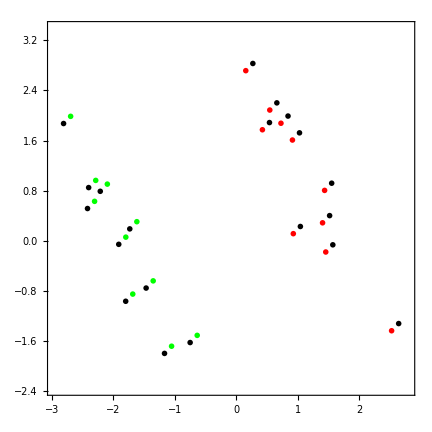

```mathematica
range=1.1Max[Table[maxs⟦i⟧-mins⟦i⟧,{i,1,Dimensions[X]⟦2⟧}]];
labelShift=0.02range;
plotRange=Table[{0.5(maxs⟦i⟧+mins⟦i⟧)-0.5range,0.5(maxs⟦i⟧+mins⟦i⟧)+0.5range},{i,1,Dimensions[X]⟦2⟧}];
dataPlot=Show[
ListPlot[{XNeg,XPos},PlotStyle->{{AbsolutePointSize[4],Green},{AbsolutePointSize[4],Red}},Frame->True,Axes->False,AspectRatio->1,
ImageSize->72 6,PlotRange->plotRange],
Graphics[Table[Text[MaTeX["\\mathbf{x}_{-"<>ToString[i]<>"}"],XNeg⟦i⟧-labelShift],{i,1,mNeg}]],
Graphics[Table[Text[MaTeX["\\mathbf{x}_{"<>ToString[j]<>"}"],XPos⟦j⟧+labelShift],{j,1,mPos}]]
]
```

```mathematica
AbsoluteTiming[brpResult=BoostedRandomPlanes[X,y,0,100]]
```

BOOSTED RANDOM PLANES...

BOOSTED RANDOM PLANES DONE.

{0.000339,{0.205811,0.881995,0.471258}}

```mathematica
brpV=brpResult⟦Range[2,Length[brpResult]]⟧;
brpV0=brpResult⟦1⟧;
brpτ=Margin[X,y,brpV,brpV0]
```

1.06995

```mathematica
AbsoluteTiming[brpfResult=BoostedRandomPlanesFast[X,y,0,1000,100,0.05]]
```

BOOSTED RANDOM PLANES FAST...

[TRIMMING DOWN TO {2, 1} SUPPORT VECTORS.]

BOOSTED RANDOM PLANES FAST DONE.

{0.0021985,{0.207031,0.879783,0.475376}}

```mathematica
brpfV=brpfResult⟦Range[2,Length[brpfResult]]⟧;
brpfV0=brpfResult⟦1⟧;
brpfτ=Margin[X,y,brpfV,brpfV0]
```

1.07355

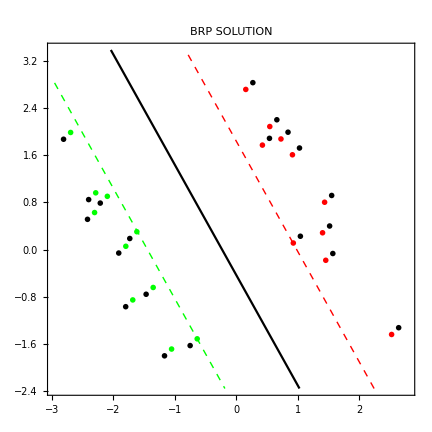

```mathematica
brpPlot=ContourPlot[{brpV0+brpV.{x1,x2}==0.0,brpV0+brpV.{x1,x2}==-brpτ,brpV0+brpV.{x1,x2}==brpτ},
{x1,plotRange⟦1,1⟧,plotRange⟦1,2⟧},{x2,plotRange⟦2,1⟧,plotRange⟦2,2⟧},ContourStyle->{Black,{Dashed,Thin,Green},{Dashed,Thin,Red}}
];
brpPlotAll=Show[brpPlot,dataPlot,ImageSize->72 6,PlotLabel->"BRP SOLUTION"]
```

```mathematica
T=100;
{brpVInfo,brpV0Info,wNegHistory,wPosHistory,events,solutionHistory}=BoostedRandomPlanesInformative[X,y,0,T];
```

BOOSTED RANDOM PLANES INFORMATIVE...

BOOSTED RANDOM PLANES INFORMATIVE DONE.

```mathematica
suppRatio=0.05;
eventsTotal=Total[events,{1}]/T;
eventsSupp=Position[eventsTotal,x_/;x>suppRatio];
wNegSupp=Union[eventsSupp⟦All,1⟧];
wPosSupp=Union[eventsSupp⟦All,2⟧];
wNegNonSupp=Complement[Range[mNeg],wNegSupp];
wPosNonSupp=Complement[Range[mPos],wPosSupp];
freqNeg=Total[eventsTotal,{2}];
freqPos=Total[eventsTotal,{1}];
brpτInfo=Margin[X,y,brpVInfo,brpV0Info];
```

```mathematica
brpPlotTemp=Show[
ContourPlot[{brpV0Info+brpVInfo.{x1,x2}==0.0,
brpV0Info+brpVInfo.{x1,x2}==-brpτInfo,
brpV0Info+brpVInfo.{x1,x2}==brpτInfo},
{x1,plotRange⟦1,1⟧,plotRange⟦1,2⟧},{x2,plotRange⟦2,1⟧,plotRange⟦2,2⟧},ContourStyle->{Black,{Dashed,Thin,Green},{Dashed,Thin,Red}}
],
Table[Graphics[{Green,Opacity[0.1],Disk[XNeg⟦i⟧,freqNeg⟦i⟧]}],{i,1,mNeg}],
Table[Graphics[{Red,Opacity[0.1],Disk[XPos⟦i⟧,freqPos⟦i⟧]}],{i,1,mPos}],
dataPlot,
ImageSize->72 6,PlotLabel->"BRP SOLUTION AT ROUND "<>ToString[T]
]
```

-Graphics-

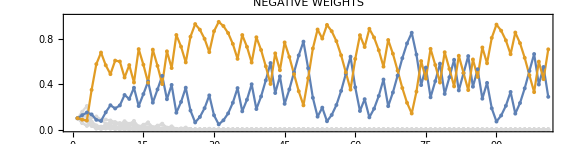

```mathematica
wNegPlot=Show[
ListPlot[Transpose[wNegHistory⟦All,wNegNonSupp⟧],Joined->True,
Frame->True,PlotRange->{{0,T},{0.0,1.0}},ImageSize->72 8,PlotStyle->LightGray,PlotMarkers->Graphics[{Disk[]},ImageSize->4]
],
ListPlot[Transpose[wNegHistory⟦All,wNegSupp⟧],Joined->True,
Frame->True,PlotRange->{{0,T},{0.0,1.0}},ImageSize->72 8,PlotMarkers->Graphics[{Disk[]},ImageSize->4],PlotLegends->Map[MaTeX["\\mathbf{x}_{-"<>ToString[#]<>"}"]&,wNegSupp]
],
AspectRatio->1/4,PlotLabel->"NEGATIVE WEIGHTS"
]
```

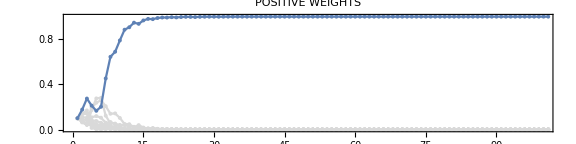

```mathematica
wPosPlot=Show[
ListPlot[Transpose[wPosHistory⟦All,wPosNonSupp⟧],Joined->True,
Frame->True,PlotRange->{{0,T},{0.0,1.0}},ImageSize->72 8,PlotStyle->LightGray,PlotMarkers->Graphics[{Disk[]},ImageSize->4]
],
ListPlot[Transpose[wPosHistory⟦All,wPosSupp⟧],Joined->True,
Frame->True,PlotRange->{{0,T},{0.0,1.0}},ImageSize->72 8,PlotMarkers->Graphics[{Disk[]},ImageSize->4],PlotLegends->Map[MaTeX["\\mathbf{x}_{"<>ToString[#]<>"}"]&,wPosSupp]
],
AspectRatio->1/4,PlotLabel->"POSITIVE WEIGHTS"
]
```

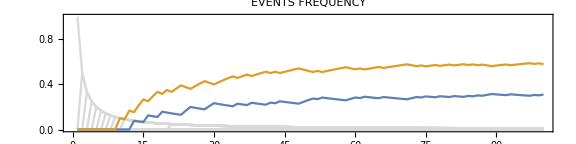

```mathematica
eventsCum=Table[Total[Take[events,t]/(t-1),{1}],{t,2,Dimensions[events]⟦1⟧}];
eventsPlot=Show[
ListPlot[Flatten[Table[eventsCum⟦All,i,j⟧,{i,wNegNonSupp},{j,wPosNonSupp}],{1,2}],
Joined->True,Frame->True,PlotRange->{{0,T},{0.0,1.0}},ImageSize->72 8,PlotStyle->LightGray],
ListPlot[Flatten[Table[eventsCum⟦All,i,j⟧,{i,wNegNonSupp},{j,wPosSupp}],{1,2}],
Joined->True,Frame->True,PlotRange->{{0,T},{0.0,1.0}},ImageSize->72 8,PlotStyle->LightGray],
ListPlot[Flatten[Table[eventsCum⟦All,i,j⟧,{i,wNegSupp},{j,wPosNonSupp}],{1,2}],
Joined->True,Frame->True,PlotRange->{{0,T},{0.0,1.0}},ImageSize->72 8,PlotStyle->LightGray],
ListPlot[Flatten[Table[eventsCum⟦All,i,j⟧,{i,wNegSupp},{j,wPosSupp}],{1,2}],
Joined->True,Frame->True,PlotRange->{{0,T},{0.0,1.0}},
PlotLegends->Flatten[Table[MaTeX["(-"<>ToString[i]<>","<>ToString[j]<>")"],{i,wNegSupp},{j,wPosSupp}],{1,2}],ImageSize->72 8],
AspectRatio->1/4,PlotLabel->"EVENTS FREQUENCY"
]
```

```mathematica
TimeConstrained[AbsoluteTiming[svmResult=SVM[X,y]],60]
```

{0.572749,{0.192883,0.819437,0.442859}}

```mathematica
svmV=svmResult⟦Range[2,Length[svmResult]]⟧;
svmV0=svmResult⟦1⟧;
svmτ=Margin[X,y,svmV,svmV0]
```

1.07359

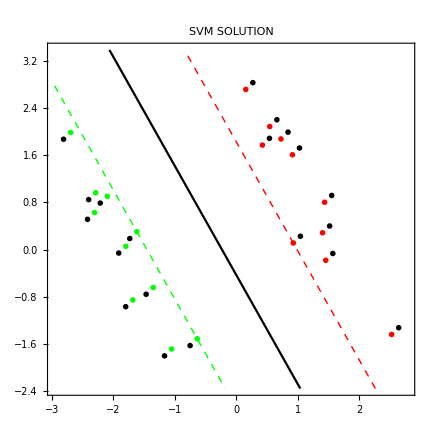

```mathematica
svmPlot=ContourPlot[{svmV0+svmV.{x1,x2}==0.0,svmV0+svmV.{x1,x2}==-1.0,svmV0+svmV.{x1,x2}==1.0},
{x1,plotRange⟦1,1⟧,plotRange⟦1,2⟧},{x2,plotRange⟦2,1⟧,plotRange⟦2,2⟧},ContourStyle->{Black,{Dashed,Thin,Green},{Dashed,Thin,Red}}
];
svmPlotAll=Show[svmPlot,dataPlot,ImageSize->72 6,PlotLabel->"SVM SOLUTION"]
```

```mathematica
CompareSolutions[brpV,brpV0,svmV,svmV0,X,y]
```

BRP VS SVM COMPARISON OF SOLUTIONS...

NORM OF DIFFERENCE: 0.00481701

RATIO OF MARGINS: 0.99661

{0.00481701,0.99661}

```mathematica
TimeConstrained[AbsoluteTiming[svmdResult=SVMDual[X,y,0.0]],60]
```

[SUPPORT VECTORS COUNTS: {2, 1}]

{3.39033,{0.192959,0.819502,0.442955}}

```mathematica
svmdV=svmdResult⟦Range[2,Length[svmdResult]]⟧;
svmdV0=svmdResult⟦1⟧;
svmdτ=Margin[X,y,svmdV,svmdV0]
```

1.07348

### Normals 3D small (with visualizations)

```mathematica
<<MaTeX`
```

```mathematica
SeedRandom[3];
m=50;
mNeg=0.5 m;
mPos=0.5 m;
XNeg=RandomVariate[MultinormalDistribution[{-1.0,0,0},0.05{{1.0,0.0,0.0},{0.0,10.0,0.0},{0.0,0.0,10.0}}],mNeg];
XPos=RandomVariate[MultinormalDistribution[{1.0,0,0},0.05{{1.0,0.0,0.0},{0.0,10.0,0.0},{0.0,0.0,10.0}}],mPos];
X=Join[XNeg,XPos];
{m,n}=Dimensions[X];
y=Table[-1,m];
y⟦Range[mPos+1,m]⟧=1;
mins=Table[Min[X⟦All,k⟧],{k,1,Dimensions[X]⟦2⟧}];
maxs=Table[Max[X⟦All,k⟧],{k,1,Dimensions[X]⟦2⟧}];
```

```mathematica
Xy=Transpose[Join[Transpose[X],{y}]];
Export[NotebookDirectory[]<>"../data/normals3d_small.txt",Xy,"Table"]
```

C:\iis\Articles\paper_50_boosted_random_planes\mathematica\../data/normals3d_small.txt

```mathematica
range=1.1Max[Table[maxs⟦i⟧-mins⟦i⟧,{i,1,Dimensions[X]⟦2⟧}]];
labelShift=0.02range;
plotRange=Table[{0.5(maxs⟦i⟧+mins⟦i⟧)-0.5range,0.5(maxs⟦i⟧+mins⟦i⟧)+0.5range},{i,1,Dimensions[X]⟦2⟧}];
dataPlot=Show[
ListPointPlot3D[{XNeg,XPos},Filling->Bottom,FillingStyle->Lighter[Lighter[Gray]],PlotStyle->{{AbsolutePointSize[4],Green},{AbsolutePointSize[4],Red}},
Boxed->True,BoxRatios->{1,1,1},ImageSize->72 6,PlotRange->plotRange],
Graphics3D[Table[Text[MaTeX["\\mathbf{x}_{-"<>ToString[i]<>"}"],XNeg⟦i⟧-labelShift],{i,1,mNeg}]],
Graphics3D[Table[Text[MaTeX["\\mathbf{x}_{"<>ToString[j]<>"}"],XPos⟦j⟧+labelShift],{j,1,mPos}]]
]
```

-Graphics3D-

```mathematica
AbsoluteTiming[brpResult=BoostedRandomPlanes[X,y,0,100]]
```

BOOSTED RANDOM PLANES...

BOOSTED RANDOM PLANES DONE.

{0.0003326,{-0.0325981,0.995299,-0.0867486,-0.0430542}}

```mathematica
brpV=brpResult⟦Range[2,Length[brpResult]]⟧;
brpV0=brpResult⟦1⟧;
brpτ=Margin[X,y,brpV,brpV0]
```

0.606099

```mathematica
AbsoluteTiming[brpfResult=BoostedRandomPlanesFast[X,y,0,1000,100,0.05]]
```

BOOSTED RANDOM PLANES FAST...

[TRIMMING DOWN TO {2, 3} SUPPORT VECTORS.]

BOOSTED RANDOM PLANES FAST DONE.

{0.0015748,{-0.0325404,0.994093,-0.0999736,-0.0422521}}

```mathematica
brpfV=brpfResult⟦Range[2,Length[brpfResult]]⟧;
brpfV0=brpfResult⟦1⟧;
brpfτ=Margin[X,y,brpfV,brpfV0]
```

0.612372

```mathematica
brpPlot=ContourPlot3D[{brpV0+brpV.{x1,x2,x3}==0.0,brpV0+brpV.{x1,x2,x3}==-brpτ,brpV0+brpV.{x1,x2,x3}==brpτ},
{x1,mins⟦1⟧,maxs⟦1⟧},{x2,mins⟦2⟧,maxs⟦2⟧},{x3,mins⟦3⟧,maxs⟦3⟧},ContourStyle->{{Directive[Black,Opacity[0.25]]},{Directive[Green,Opacity[0.25]]},{Directive[Red,Opacity[0.25]]}},
Mesh->None,ViewPoint->{0.25,-3,1},ViewProjection->"Perspective"
];
brpPlotAll=Show[brpPlot,dataPlot,ImageSize->72 6,PlotLabel->"BRP SOLUTION",
Boxed->True,BoxRatios->{1,1,1},ImageSize->72 6,PlotRange->plotRange,ViewPoint->{0.25,-3,1},ViewProjection->"Perspective"]
```

-Graphics3D-

```mathematica
T=100;
{brpVInfo,brpV0Info,wNegHistory,wPosHistory,events,solutionHistory}=BoostedRandomPlanesInformative[X,y,0,T];
```

BOOSTED RANDOM PLANES INFORMATIVE...

BOOSTED RANDOM PLANES INFORMATIVE DONE.

```mathematica
suppRatio=0.05;
eventsTotal=Total[events,{1}]/T;
eventsSupp=Position[eventsTotal,x_/;x>suppRatio];
wNegSupp=Union[eventsSupp⟦All,1⟧];
wPosSupp=Union[eventsSupp⟦All,2⟧];
wNegNonSupp=Complement[Range[mNeg],wNegSupp];
wPosNonSupp=Complement[Range[mPos],wPosSupp];
freqNeg=Total[eventsTotal,{2}];
freqPos=Total[eventsTotal,{1}];
brpτInfo=Margin[X,y,brpVInfo,brpV0Info];
```

```mathematica
brpPlotTemp=Show[
ContourPlot3D[{brpV0Info+brpVInfo.{x1,x2,x3}==0.0,
brpV0Info+brpVInfo.{x1,x2,x3}==-brpτInfo,
brpV0Info+brpVInfo.{x1,x2,x3}==brpτInfo},
{x1,mins⟦1⟧,maxs⟦1⟧},{x2,mins⟦2⟧,maxs⟦2⟧},{x3,mins⟦3⟧,maxs⟦3⟧},ContourStyle->{{Directive[Black,Opacity[0.25]]},{Directive[Green,Opacity[0.25]]},{Directive[Red,Opacity[0.25]]}},
Mesh->None
],
Table[Graphics3D[{Green,Opacity[0.1],Ball[XNeg⟦i⟧,freqNeg⟦i⟧]}],{i,1,mNeg}],
Table[Graphics3D[{Red,Opacity[0.1],Ball[XPos⟦i⟧,freqPos⟦i⟧]}],{i,1,mPos}],
dataPlot,
ImageSize->72 6,PlotLabel->"BRP SOLUTION AT ROUND "<>ToString[T],
Boxed->True,BoxRatios->{1,1,1},ImageSize->72 6,PlotRange->plotRange,
ViewPoint->{0.25,-3,1},ViewProjection->"Perspective"
]
```

-Graphics3D-

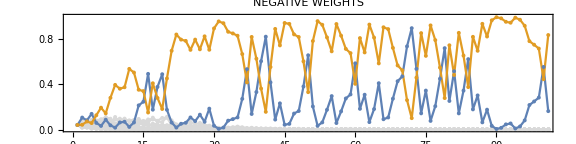

```mathematica
wNegPlot=Show[
ListPlot[Transpose[wNegHistory⟦All,wNegNonSupp⟧],Joined->True,
Frame->True,PlotRange->{{0,T},{0.0,1.0}},ImageSize->72 8,PlotStyle->LightGray,PlotMarkers->Graphics[{Disk[]},ImageSize->4]
],
ListPlot[Transpose[wNegHistory⟦All,wNegSupp⟧],Joined->True,
Frame->True,PlotRange->{{0,T},{0.0,1.0}},ImageSize->72 8,PlotMarkers->Graphics[{Disk[]},ImageSize->4],PlotLegends->Map[MaTeX["\\mathbf{x}_{-"<>ToString[#]<>"}"]&,wNegSupp]
],
AspectRatio->1/4,PlotLabel->"NEGATIVE WEIGHTS"
]
```

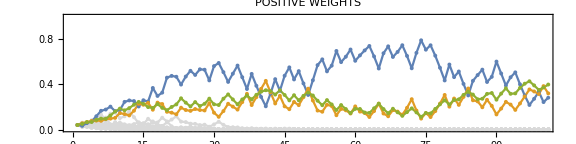

```mathematica
wPosPlot=Show[
ListPlot[Transpose[wPosHistory⟦All,wPosNonSupp⟧],Joined->True,
Frame->True,PlotRange->{{0,T},{0.0,1.0}},ImageSize->72 8,PlotStyle->LightGray,PlotMarkers->Graphics[{Disk[]},ImageSize->4]
],
ListPlot[Transpose[wPosHistory⟦All,wPosSupp⟧],Joined->True,
Frame->True,PlotRange->{{0,T},{0.0,1.0}},ImageSize->72 8,PlotMarkers->Graphics[{Disk[]},ImageSize->4],PlotLegends->Map[MaTeX["\\mathbf{x}_{"<>ToString[#]<>"}"]&,wPosSupp]
],
AspectRatio->1/4,PlotLabel->"POSITIVE WEIGHTS"
]
```

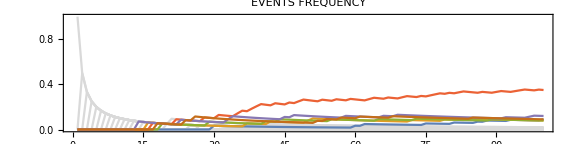

```mathematica
eventsCum=Table[Total[Take[events,t]/(t-1),{1}],{t,2,Dimensions[events]⟦1⟧}];
eventsPlot=Show[
ListPlot[Flatten[Table[eventsCum⟦All,i,j⟧,{i,wNegNonSupp},{j,wPosNonSupp}],{1,2}],
Joined->True,Frame->True,PlotRange->{{0,T},{0.0,1.0}},ImageSize->72 8,PlotStyle->LightGray],
ListPlot[Flatten[Table[eventsCum⟦All,i,j⟧,{i,wNegNonSupp},{j,wPosSupp}],{1,2}],
Joined->True,Frame->True,PlotRange->{{0,T},{0.0,1.0}},ImageSize->72 8,PlotStyle->LightGray],
ListPlot[Flatten[Table[eventsCum⟦All,i,j⟧,{i,wNegSupp},{j,wPosNonSupp}],{1,2}],
Joined->True,Frame->True,PlotRange->{{0,T},{0.0,1.0}},ImageSize->72 8,PlotStyle->LightGray],
ListPlot[Flatten[Table[eventsCum⟦All,i,j⟧,{i,wNegSupp},{j,wPosSupp}],{1,2}],
Joined->True,Frame->True,PlotRange->{{0,T},{0.0,1.0}},
PlotLegends->Flatten[Table[MaTeX["(-"<>ToString[i]<>","<>ToString[j]<>")"],{i,wNegSupp},{j,wPosSupp}],{1,2}],ImageSize->72 8],
AspectRatio->1/4,PlotLabel->"EVENTS FREQUENCY"
]
```

```mathematica
TimeConstrained[AbsoluteTiming[svmResult=SVM[X,y]],60]
```

{1.68896,{-0.0546534,1.62078,-0.161366,-0.0730063}}

```mathematica
svmV=svmResult⟦Range[2,Length[svmResult]]⟧;
svmV0=svmResult⟦1⟧;
svmτ=Margin[X,y,svmV,svmV0]
```

0.613334

```mathematica
svmPlot=ContourPlot3D[{svmV0+svmV.{x1,x2,x3}==0.0,svmV0+svmV.{x1,x2,x3}==-1.0,svmV0+svmV.{x1,x2,x3}==1.0},
{x1,mins⟦1⟧,maxs⟦1⟧},{x2,mins⟦2⟧,maxs⟦2⟧},{x3,mins⟦3⟧,maxs⟦3⟧},ContourStyle->{{Directive[Black,Opacity[0.25]]},{Directive[Green,Opacity[0.25]]},{Directive[Red,Opacity[0.25]]}},
Mesh->None
];
svmPlotAll=Show[svmPlot,dataPlot,ImageSize->72 6,PlotLabel->"SVM SOLUTION",
Boxed->True,BoxRatios->{1,1,1},ImageSize->72 6,PlotRange->plotRange,ViewPoint->{0.25,-3,1},ViewProjection->"Perspective"]
```

-Graphics3D-

```mathematica
CompareSolutions[brpV,brpV0,svmV,svmV0,X,y]
```

BRP VS SVM COMPARISON OF SOLUTIONS...

NORM OF DIFFERENCE: 0.0124307

RATIO OF MARGINS: 0.988204

{0.0124307,0.988204}

```mathematica
TimeConstrained[AbsoluteTiming[svmdResult=SVMDual[X,y,0.01]],60]
```

$Aborted

### Test case A (with visualizations)

```mathematica
<<MaTeX`
```

```mathematica
XNeg={{-1.0,0.0}};
XPos={{1.0,-1.0},{1.0,2.0}};
X=Join[XNeg,XPos];
y={-1,1,1};
{m,n}=Dimensions[X];
mNeg=Length[XNeg];
mPos=Length[XPos];
mins=Table[Min[X⟦All,k⟧],{k,1,Dimensions[X]⟦2⟧}];
maxs=Table[Max[X⟦All,k⟧],{k,1,Dimensions[X]⟦2⟧}];
```

```mathematica
Xy=Transpose[Join[Transpose[X],{y}]];
Export[NotebookDirectory[]<>"../data/testcase_a.txt",Xy,"Table"]
```

C:\iis\Articles\paper_50_boosted_random_planes\mathematica\../data/testcase_a.txt

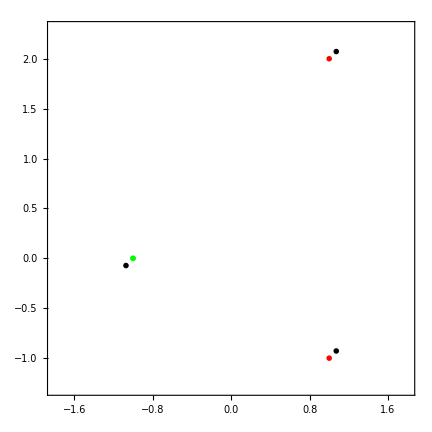

```mathematica
range=1.2Max[Table[maxs⟦i⟧-mins⟦i⟧,{i,1,Dimensions[X]⟦2⟧}]];
labelShift=0.02range;
plotRange=Table[{0.5(maxs⟦i⟧+mins⟦i⟧)-0.5range,0.5(maxs⟦i⟧+mins⟦i⟧)+0.5range},{i,1,Dimensions[X]⟦2⟧}];
dataPlot=Show[
ListPlot[{XNeg,XPos},PlotStyle->{{AbsolutePointSize[4],Green},{AbsolutePointSize[4],Red}},Frame->True,Axes->False,AspectRatio->1,
ImageSize->72 6,PlotRange->plotRange],
Graphics[Table[Text[MaTeX["\\mathbf{x}_{-"<>ToString[i]<>"}"],XNeg⟦i⟧-labelShift],{i,1,mNeg}]],
Graphics[Table[Text[MaTeX["\\mathbf{x}_{"<>ToString[j]<>"}"],XPos⟦j⟧+labelShift],{j,1,mPos}]]
]
```

```mathematica
AbsoluteTiming[brpResult=BoostedRandomPlanes[X,y,0,1000]]
```

BOOSTED RANDOM PLANES...

BOOSTED RANDOM PLANES DONE.

{0.0015298,{-0.0000661302,1.,0.000806465}}

```mathematica
brpV=brpResult⟦Range[2,Length[brpResult]]⟧;
brpV0=brpResult⟦1⟧;
brpτ=Margin[X,y,brpV,brpV0]
```

0.999127

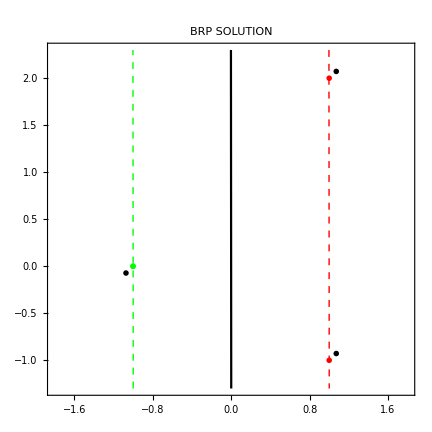

```mathematica
brpPlot=ContourPlot[{brpV0+brpV.{x1,x2}==0.0,brpV0+brpV.{x1,x2}==-brpτ,brpV0+brpV.{x1,x2}==brpτ},
{x1,plotRange⟦1,1⟧,plotRange⟦1,2⟧},{x2,plotRange⟦2,1⟧,plotRange⟦2,2⟧},ContourStyle->{Black,{Dashed,Thin,Green},{Dashed,Thin,Red}}
];
brpPlotAll=Show[brpPlot,dataPlot,ImageSize->72 6,PlotLabel->"BRP SOLUTION"]
```

```mathematica
T=100;
{brpVInfo,brpV0Info,wNegHistory,wPosHistory,events,solutionHistory}=BoostedRandomPlanesInformative[X,y,0,T];
```

BOOSTED RANDOM PLANES INFORMATIVE...

BOOSTED RANDOM PLANES INFORMATIVE DONE.

```mathematica
suppRatio=-1.0;
eventsTotal=Total[events,{1}]/T;
eventsSupp=Position[eventsTotal,x_/;x>suppRatio];
wNegAll=Union[eventsSupp⟦All,1⟧];
wPosAll=Union[eventsSupp⟦All,2⟧];
```

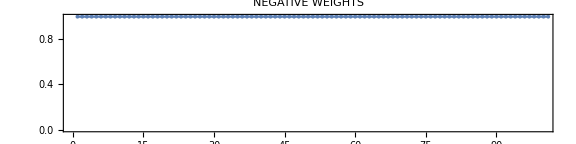

```mathematica
wNegPlot=Show[
ListPlot[Transpose[wNegHistory⟦All,wNegAll⟧],Joined->True,
Frame->True,PlotRange->{{0,T},{0.0,1.0}},ImageSize->72 8,PlotMarkers->Graphics[{Disk[]},ImageSize->4],PlotLegends->Map[MaTeX["\\mathbf{x}_{-"<>ToString[#]<>"}"]&,wNegAll]
],
AspectRatio->1/4,PlotLabel->"NEGATIVE WEIGHTS"
]
```

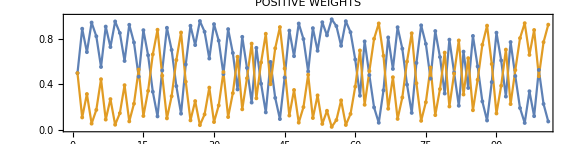

```mathematica
wPosPlot=Show[
ListPlot[Transpose[wPosHistory⟦All,wPosAll⟧],Joined->True,
Frame->True,PlotRange->{{0,T},{0.0,1.0}},ImageSize->72 8,PlotMarkers->Graphics[{Disk[]},ImageSize->4],PlotLegends->Map[MaTeX["\\mathbf{x}_{"<>ToString[#]<>"}"]&,wPosAll]
],
AspectRatio->1/4,PlotLabel->"POSITIVE WEIGHTS"
]
```

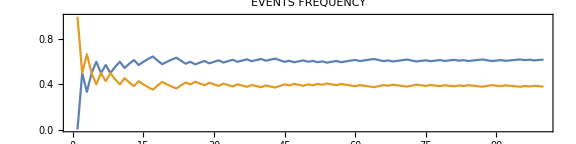

```mathematica
eventsCum=Table[Total[Take[events,t]/(t-1),{1}],{t,2,Dimensions[events]⟦1⟧}];
eventsPlot=Show[
ListPlot[Flatten[Table[eventsCum⟦All,i,j⟧,{i,wNegAll},{j,wPosAll}],{1,2}],
Joined->True,Frame->True,PlotRange->{{0,T},{0.0,1.0}},
PlotLegends->Flatten[Table[MaTeX["(-"<>ToString[i]<>","<>ToString[j]<>")"],{i,wNegAll},{j,wPosAll}],{1,2}],ImageSize->72 8],
AspectRatio->1/4,PlotLabel->"EVENTS FREQUENCY"
]
```

### Test case B (with visualizations)

```mathematica
<<MaTeX`
```

```mathematica
XNeg={{-1.0,0.0}};
XPos={{1.0,-1.0},{1.0,0.0},{1.0,2.0}};
X=Join[XNeg,XPos];
y={-1,1,1,1};
{m,n}=Dimensions[X];
mNeg=Length[XNeg];
mPos=Length[XPos];
mins=Table[Min[X⟦All,k⟧],{k,1,Dimensions[X]⟦2⟧}];
maxs=Table[Max[X⟦All,k⟧],{k,1,Dimensions[X]⟦2⟧}];
```

```mathematica
Xy=Transpose[Join[Transpose[X],{y}]];
Export[NotebookDirectory[]<>"../data/testcase_b.txt",Xy,"Table"]
```

C:\iis\Articles\paper_50_boosted_random_planes\mathematica\../data/testcase_b.txt

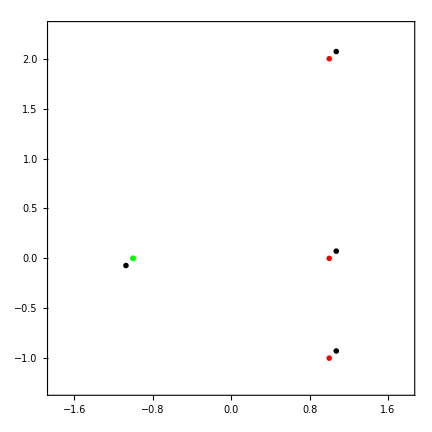

```mathematica
range=1.2Max[Table[maxs⟦i⟧-mins⟦i⟧,{i,1,Dimensions[X]⟦2⟧}]];
labelShift=0.02range;
plotRange=Table[{0.5(maxs⟦i⟧+mins⟦i⟧)-0.5range,0.5(maxs⟦i⟧+mins⟦i⟧)+0.5range},{i,1,Dimensions[X]⟦2⟧}];
dataPlot=Show[
ListPlot[{XNeg,XPos},PlotStyle->{{AbsolutePointSize[4],Green},{AbsolutePointSize[4],Red}},Frame->True,Axes->False,AspectRatio->1,
ImageSize->72 6,PlotRange->plotRange],
Graphics[Table[Text[MaTeX["\\mathbf{x}_{-"<>ToString[i]<>"}"],XNeg⟦i⟧-labelShift],{i,1,mNeg}]],
Graphics[Table[Text[MaTeX["\\mathbf{x}_{"<>ToString[j]<>"}"],XPos⟦j⟧+labelShift],{j,1,mPos}]]
]
```

```mathematica
AbsoluteTiming[brpResult=BoostedRandomPlanes[X,y,0,1000]]
```

BOOSTED RANDOM PLANES...

BOOSTED RANDOM PLANES DONE.

{0.00241303,{-0.0000355061,1.,0.000639749}}

```mathematica
brpV=brpResult⟦Range[2,Length[brpResult]]⟧;
brpV0=brpResult⟦1⟧;
brpτ=Margin[X,y,brpV,brpV0]
```

0.999325

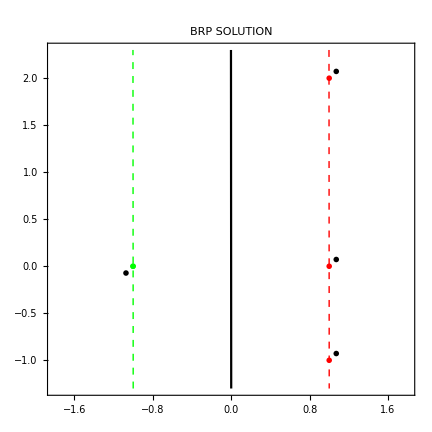

```mathematica
brpPlot=ContourPlot[{brpV0+brpV.{x1,x2}==0.0,brpV0+brpV.{x1,x2}==-brpτ,brpV0+brpV.{x1,x2}==brpτ},
{x1,plotRange⟦1,1⟧,plotRange⟦1,2⟧},{x2,plotRange⟦2,1⟧,plotRange⟦2,2⟧},ContourStyle->{Black,{Dashed,Thin,Green},{Dashed,Thin,Red}}
];
brpPlotAll=Show[brpPlot,dataPlot,ImageSize->72 6,PlotLabel->"BRP SOLUTION"]
```

```mathematica
T=100;
{brpVInfo,brpV0Info,wNegHistory,wPosHistory,events,solutionHistory}=BoostedRandomPlanesInformative[X,y,0,T];
```

BOOSTED RANDOM PLANES INFORMATIVE...

BOOSTED RANDOM PLANES INFORMATIVE DONE.

```mathematica
suppRatio=-1.0;
eventsTotal=Total[events,{1}]/T;
eventsSupp=Position[eventsTotal,x_/;x>suppRatio];
wNegAll=Union[eventsSupp⟦All,1⟧];
wPosAll=Union[eventsSupp⟦All,2⟧];
```

```mathematica
wNegPlot=Show[
ListPlot[Transpose[wNegHistory⟦All,wNegAll⟧],Joined->True,
Frame->True,PlotRange->{{0,T},{0.0,1.0}},ImageSize->72 8,PlotMarkers->Graphics[{Disk[]},ImageSize->4],PlotLegends->Map[MaTeX["\\mathbf{x}_{-"<>ToString[#]<>"}"]&,wNegAll]
],
AspectRatio->1/4,PlotLabel->"NEGATIVE WEIGHTS"
]
```

-Graphics-

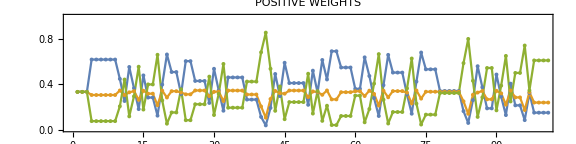

```mathematica
wPosPlot=Show[
ListPlot[Transpose[wPosHistory⟦All,wPosAll⟧],Joined->True,
Frame->True,PlotRange->{{0,T},{0.0,1.0}},ImageSize->72 8,PlotMarkers->Graphics[{Disk[]},ImageSize->4],PlotLegends->Map[MaTeX["\\mathbf{x}_{"<>ToString[#]<>"}"]&,wPosAll]
],
AspectRatio->1/4,PlotLabel->"POSITIVE WEIGHTS"
]
```

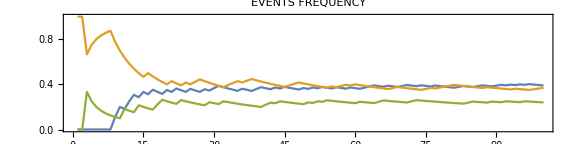

```mathematica
eventsCum=Table[Total[Take[events,t]/(t-1),{1}],{t,2,Dimensions[events]⟦1⟧}];
eventsPlot=Show[
ListPlot[Flatten[Table[eventsCum⟦All,i,j⟧,{i,wNegAll},{j,wPosAll}],{1,2}],
Joined->True,Frame->True,PlotRange->{{0,T},{0.0,1.0}},
PlotLegends->Flatten[Table[MaTeX["(-"<>ToString[i]<>","<>ToString[j]<>")"],{i,wNegAll},{j,wPosAll}],{1,2}],ImageSize->72 8],
AspectRatio->1/4,PlotLabel->"EVENTS FREQUENCY"
]
```

### Test case C (with visualizations)

```mathematica
<<MaTeX`
```

```mathematica
XNeg={{-1.0,0.0}};
XPos={{1.1,-1.0},{1.0,0.0},{1.0,2.0}};
X=Join[XNeg,XPos];
y={-1,1,1,1};
{m,n}=Dimensions[X];
mNeg=Length[XNeg];
mPos=Length[XPos];
mins=Table[Min[X⟦All,k⟧],{k,1,Dimensions[X]⟦2⟧}];
maxs=Table[Max[X⟦All,k⟧],{k,1,Dimensions[X]⟦2⟧}];
```

```mathematica
Xy=Transpose[Join[Transpose[X],{y}]];
Export[NotebookDirectory[]<>"../data/testcase_c.txt",Xy,"Table"]
```

C:\iis\Articles\paper_50_boosted_random_planes\mathematica\../data/testcase_c.txt

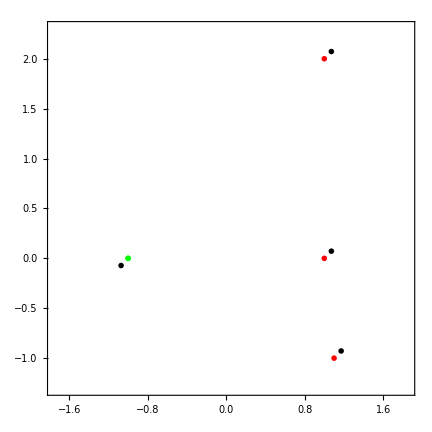

```mathematica
range=1.2Max[Table[maxs⟦i⟧-mins⟦i⟧,{i,1,Dimensions[X]⟦2⟧}]];
labelShift=0.02range;
plotRange=Table[{0.5(maxs⟦i⟧+mins⟦i⟧)-0.5range,0.5(maxs⟦i⟧+mins⟦i⟧)+0.5range},{i,1,Dimensions[X]⟦2⟧}];
dataPlot=Show[
ListPlot[{XNeg,XPos},PlotStyle->{{AbsolutePointSize[4],Green},{AbsolutePointSize[4],Red}},Frame->True,Axes->False,AspectRatio->1,
ImageSize->72 6,PlotRange->plotRange],
Graphics[Table[Text[MaTeX["\\mathbf{x}_{-"<>ToString[i]<>"}"],XNeg⟦i⟧-labelShift],{i,1,mNeg}]],
Graphics[Table[Text[MaTeX["\\mathbf{x}_{"<>ToString[j]<>"}"],XPos⟦j⟧+labelShift],{j,1,mPos}]]
]
```

```mathematica
AbsoluteTiming[brpResult=BoostedRandomPlanes[X,y,0,1000]]
```

BOOSTED RANDOM PLANES...

BOOSTED RANDOM PLANES DONE.

{0.00164285,{-0.000232606,0.999989,0.00465827}}

```mathematica
brpV=brpResult⟦Range[2,Length[brpResult]]⟧;
brpV0=brpResult⟦1⟧;
brpτ=Margin[X,y,brpV,brpV0]
```

0.999757

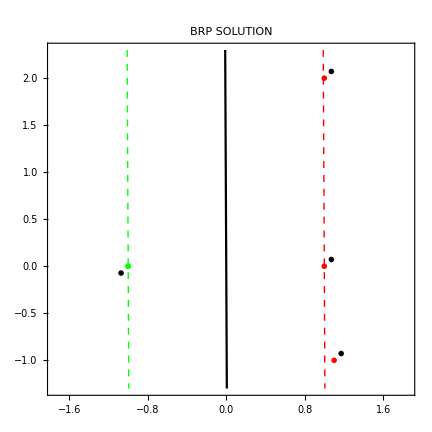

```mathematica
brpPlot=ContourPlot[{brpV0+brpV.{x1,x2}==0.0,brpV0+brpV.{x1,x2}==-brpτ,brpV0+brpV.{x1,x2}==brpτ},
{x1,plotRange⟦1,1⟧,plotRange⟦1,2⟧},{x2,plotRange⟦2,1⟧,plotRange⟦2,2⟧},ContourStyle->{Black,{Dashed,Thin,Green},{Dashed,Thin,Red}}
];
brpPlotAll=Show[brpPlot,dataPlot,ImageSize->72 6,PlotLabel->"BRP SOLUTION"]
```

```mathematica
T=100;
{brpVInfo,brpV0Info,wNegHistory,wPosHistory,events,solutionHistory}=BoostedRandomPlanesInformative[X,y,0,T];
```

BOOSTED RANDOM PLANES INFORMATIVE...

BOOSTED RANDOM PLANES INFORMATIVE DONE.

```mathematica
suppRatio=-1.0;
eventsTotal=Total[events,{1}]/T;
eventsSupp=Position[eventsTotal,x_/;x>suppRatio];
wNegAll=Union[eventsSupp⟦All,1⟧];
wPosAll=Union[eventsSupp⟦All,2⟧];
```

```mathematica
wNegPlot=Show[
ListPlot[Transpose[wNegHistory⟦All,wNegAll⟧],Joined->True,
Frame->True,PlotRange->{{0,T},{0.0,1.0}},ImageSize->72 8,PlotMarkers->Graphics[{Disk[]},ImageSize->4],PlotLegends->Map[MaTeX["\\mathbf{x}_{-"<>ToString[#]<>"}"]&,wNegAll]
],
AspectRatio->1/4,PlotLabel->"NEGATIVE WEIGHTS"
]
```

-Graphics-

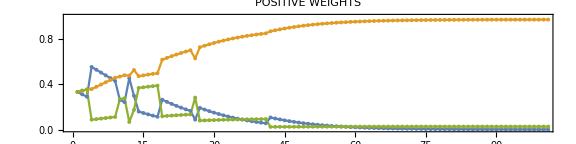

```mathematica
wPosPlot=Show[
ListPlot[Transpose[wPosHistory⟦All,wPosAll⟧],Joined->True,
Frame->True,PlotRange->{{0,T},{0.0,1.0}},ImageSize->72 8,PlotMarkers->Graphics[{Disk[]},ImageSize->4],PlotLegends->Map[MaTeX["\\mathbf{x}_{"<>ToString[#]<>"}"]&,wPosAll]
],
AspectRatio->1/4,PlotLabel->"POSITIVE WEIGHTS"
]
```

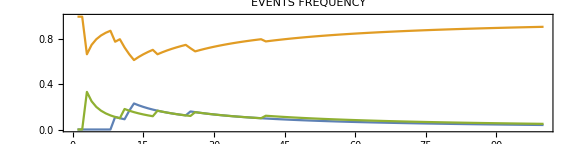

```mathematica
eventsCum=Table[Total[Take[events,t]/(t-1),{1}],{t,2,Dimensions[events]⟦1⟧}];
eventsPlot=Show[
ListPlot[Flatten[Table[eventsCum⟦All,i,j⟧,{i,wNegAll},{j,wPosAll}],{1,2}],
Joined->True,Frame->True,PlotRange->{{0,T},{0.0,1.0}},
PlotLegends->Flatten[Table[MaTeX["(-"<>ToString[i]<>","<>ToString[j]<>")"],{i,wNegAll},{j,wPosAll}],{1,2}],ImageSize->72 8],
AspectRatio->1/4,PlotLabel->"EVENTS FREQUENCY"
]
```

### Test case D (with visualizations)

```mathematica
<<MaTeX`
```

```mathematica
XNeg={{-1.0,0.0}};
XPos={{1.0,-1.0},{1.1,0.0},{1.0,2.0}};
X=Join[XNeg,XPos];
y={-1,1,1,1};
{m,n}=Dimensions[X];
mNeg=Length[XNeg];
mPos=Length[XPos];
mins=Table[Min[X⟦All,k⟧],{k,1,Dimensions[X]⟦2⟧}];
maxs=Table[Max[X⟦All,k⟧],{k,1,Dimensions[X]⟦2⟧}];
```

```mathematica
Xy=Transpose[Join[Transpose[X],{y}]];
Export[NotebookDirectory[]<>"../data/testcase_d.txt",Xy,"Table"]
```

C:\iis\Articles\paper_50_boosted_random_planes\mathematica\../data/testcase_d.txt

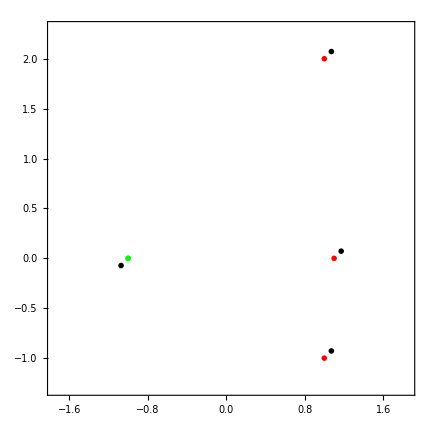

```mathematica
range=1.2Max[Table[maxs⟦i⟧-mins⟦i⟧,{i,1,Dimensions[X]⟦2⟧}]];
labelShift=0.02range;
plotRange=Table[{0.5(maxs⟦i⟧+mins⟦i⟧)-0.5range,0.5(maxs⟦i⟧+mins⟦i⟧)+0.5range},{i,1,Dimensions[X]⟦2⟧}];
dataPlot=Show[
ListPlot[{XNeg,XPos},PlotStyle->{{AbsolutePointSize[4],Green},{AbsolutePointSize[4],Red}},Frame->True,Axes->False,AspectRatio->1,
ImageSize->72 6,PlotRange->plotRange],
Graphics[Table[Text[MaTeX["\\mathbf{x}_{-"<>ToString[i]<>"}"],XNeg⟦i⟧-labelShift],{i,1,mNeg}]],
Graphics[Table[Text[MaTeX["\\mathbf{x}_{"<>ToString[j]<>"}"],XPos⟦j⟧+labelShift],{j,1,mPos}]]
]
```

```mathematica
AbsoluteTiming[brpResult=BoostedRandomPlanes[X,y,0,1000]]
```

BOOSTED RANDOM PLANES...

BOOSTED RANDOM PLANES DONE.

{0.00160419,{-0.000382501,1.,0.000401246}}

```mathematica
brpV=brpResult⟦Range[2,Length[brpResult]]⟧;
brpV0=brpResult⟦1⟧;
brpτ=Margin[X,y,brpV,brpV0]
```

0.999216

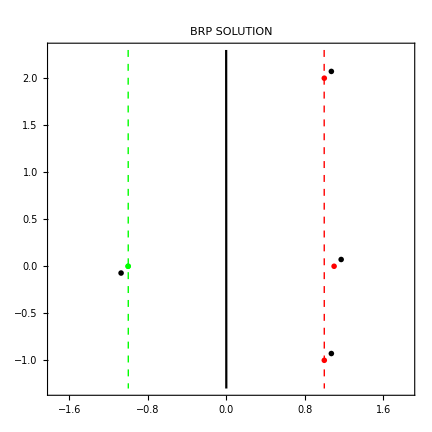

```mathematica
brpPlot=ContourPlot[{brpV0+brpV.{x1,x2}==0.0,brpV0+brpV.{x1,x2}==-brpτ,brpV0+brpV.{x1,x2}==brpτ},
{x1,plotRange⟦1,1⟧,plotRange⟦1,2⟧},{x2,plotRange⟦2,1⟧,plotRange⟦2,2⟧},ContourStyle->{Black,{Dashed,Thin,Green},{Dashed,Thin,Red}}
];
brpPlotAll=Show[brpPlot,dataPlot,ImageSize->72 6,PlotLabel->"BRP SOLUTION"]
```

```mathematica
T=100;
{brpVInfo,brpV0Info,wNegHistory,wPosHistory,events,solutionHistory}=BoostedRandomPlanesInformative[X,y,0,T];
```

BOOSTED RANDOM PLANES INFORMATIVE...

BOOSTED RANDOM PLANES INFORMATIVE DONE.

```mathematica
suppRatio=-1.0;
eventsTotal=Total[events,{1}]/T;
eventsSupp=Position[eventsTotal,x_/;x>suppRatio];
wNegAll=Union[eventsSupp⟦All,1⟧];
wPosAll=Union[eventsSupp⟦All,2⟧];
```

```mathematica
wNegPlot=Show[
ListPlot[Transpose[wNegHistory⟦All,wNegAll⟧],Joined->True,
Frame->True,PlotRange->{{0,T},{0.0,1.0}},ImageSize->72 8,PlotMarkers->Graphics[{Disk[]},ImageSize->4],PlotLegends->Map[MaTeX["\\mathbf{x}_{-"<>ToString[#]<>"}"]&,wNegAll]
],
AspectRatio->1/4,PlotLabel->"NEGATIVE WEIGHTS"
]
```

-Graphics-

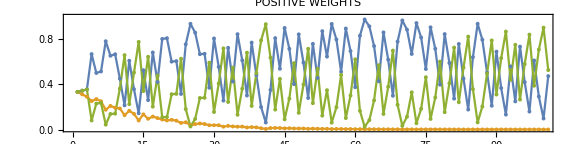

```mathematica
wPosPlot=Show[
ListPlot[Transpose[wPosHistory⟦All,wPosAll⟧],Joined->True,
Frame->True,PlotRange->{{0,T},{0.0,1.0}},ImageSize->72 8,PlotMarkers->Graphics[{Disk[]},ImageSize->4],PlotLegends->Map[MaTeX["\\mathbf{x}_{"<>ToString[#]<>"}"]&,wPosAll]
],
AspectRatio->1/4,PlotLabel->"POSITIVE WEIGHTS"
]
```

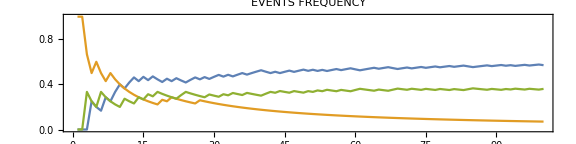

```mathematica
eventsCum=Table[Total[Take[events,t]/(t-1),{1}],{t,2,Dimensions[events]⟦1⟧}];
eventsPlot=Show[
ListPlot[Flatten[Table[eventsCum⟦All,i,j⟧,{i,wNegAll},{j,wPosAll}],{1,2}],
Joined->True,Frame->True,PlotRange->{{0,T},{0.0,1.0}},
PlotLegends->Flatten[Table[MaTeX["(-"<>ToString[i]<>","<>ToString[j]<>")"],{i,wNegAll},{j,wPosAll}],{1,2}],ImageSize->72 8],
AspectRatio->1/4,PlotLabel->"EVENTS FREQUENCY"
]
```

### Test case E (with visualizations)

```mathematica
<<MaTeX`
```

```mathematica
XNeg={{-1.0,0.0}};
XPos={{0.9,-1.0},{1.0,0.0},{1.0,2.0}};
X=Join[XNeg,XPos];
y={-1,1,1,1};
{m,n}=Dimensions[X];
mNeg=Length[XNeg];
mPos=Length[XPos];
mins=Table[Min[X⟦All,k⟧],{k,1,Dimensions[X]⟦2⟧}];
maxs=Table[Max[X⟦All,k⟧],{k,1,Dimensions[X]⟦2⟧}];
```

```mathematica
Xy=Transpose[Join[Transpose[X],{y}]];
Export[NotebookDirectory[]<>"../data/testcase_e.txt",Xy,"Table"]
```

C:\iis\Articles\paper_50_boosted_random_planes\mathematica\../data/testcase_e.txt

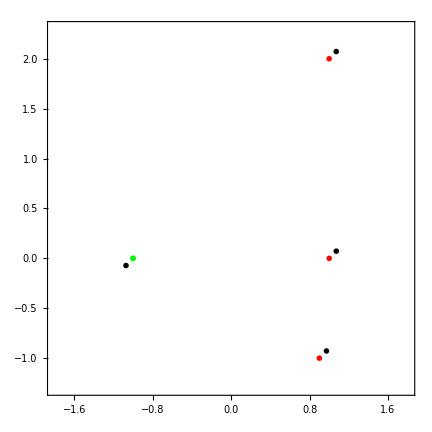

```mathematica
range=1.2Max[Table[maxs⟦i⟧-mins⟦i⟧,{i,1,Dimensions[X]⟦2⟧}]];
labelShift=0.02range;
plotRange=Table[{0.5(maxs⟦i⟧+mins⟦i⟧)-0.5range,0.5(maxs⟦i⟧+mins⟦i⟧)+0.5range},{i,1,Dimensions[X]⟦2⟧}];
dataPlot=Show[
ListPlot[{XNeg,XPos},PlotStyle->{{AbsolutePointSize[4],Green},{AbsolutePointSize[4],Red}},Frame->True,Axes->False,AspectRatio->1,
ImageSize->72 6,PlotRange->plotRange],
Graphics[Table[Text[MaTeX["\\mathbf{x}_{-"<>ToString[i]<>"}"],XNeg⟦i⟧-labelShift],{i,1,mNeg}]],
Graphics[Table[Text[MaTeX["\\mathbf{x}_{"<>ToString[j]<>"}"],XPos⟦j⟧+labelShift],{j,1,mPos}]]
]
```

```mathematica
AbsoluteTiming[brpResult=BoostedRandomPlanes[X,y,0,1000]]
```

BOOSTED RANDOM PLANES...

BOOSTED RANDOM PLANES DONE.

{0.00239115,{0.0329488,0.999481,-0.0322109}}

```mathematica
brpV=brpResult⟦Range[2,Length[brpResult]]⟧;
brpV0=brpResult⟦1⟧;
brpτ=Margin[X,y,brpV,brpV0]
```

0.964693

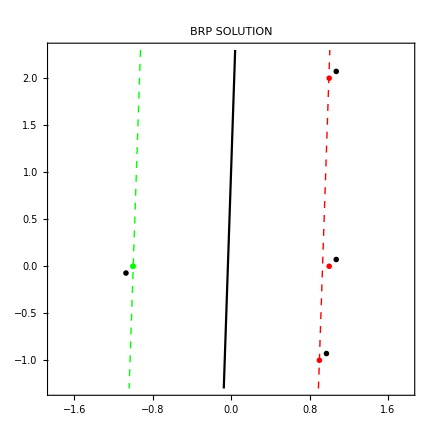

```mathematica
brpPlot=ContourPlot[{brpV0+brpV.{x1,x2}==0.0,brpV0+brpV.{x1,x2}==-brpτ,brpV0+brpV.{x1,x2}==brpτ},
{x1,plotRange⟦1,1⟧,plotRange⟦1,2⟧},{x2,plotRange⟦2,1⟧,plotRange⟦2,2⟧},ContourStyle->{Black,{Dashed,Thin,Green},{Dashed,Thin,Red}}
];
brpPlotAll=Show[brpPlot,dataPlot,ImageSize->72 6,PlotLabel->"BRP SOLUTION"]
```

```mathematica
T=100;
{brpVInfo,brpV0Info,wNegHistory,wPosHistory,events,solutionHistory}=BoostedRandomPlanesInformative[X,y,0,T];
```

BOOSTED RANDOM PLANES INFORMATIVE...

BOOSTED RANDOM PLANES INFORMATIVE DONE.

```mathematica
suppRatio=-1.0;
eventsTotal=Total[events,{1}]/T;
eventsSupp=Position[eventsTotal,x_/;x>suppRatio];
wNegAll=Union[eventsSupp⟦All,1⟧];
wPosAll=Union[eventsSupp⟦All,2⟧];
```

```mathematica
wNegPlot=Show[
ListPlot[Transpose[wNegHistory⟦All,wNegAll⟧],Joined->True,
Frame->True,PlotRange->{{0,T},{0.0,1.0}},ImageSize->72 8,PlotMarkers->Graphics[{Disk[]},ImageSize->4],PlotLegends->Map[MaTeX["\\mathbf{x}_{-"<>ToString[#]<>"}"]&,wNegAll]
],
AspectRatio->1/4,PlotLabel->"NEGATIVE WEIGHTS"
]
```

-Graphics-

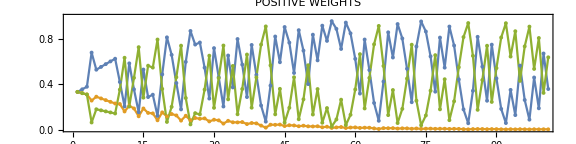

```mathematica
wPosPlot=Show[
ListPlot[Transpose[wPosHistory⟦All,wPosAll⟧],Joined->True,
Frame->True,PlotRange->{{0,T},{0.0,1.0}},ImageSize->72 8,PlotMarkers->Graphics[{Disk[]},ImageSize->4],PlotLegends->Map[MaTeX["\\mathbf{x}_{"<>ToString[#]<>"}"]&,wPosAll]
],
AspectRatio->1/4,PlotLabel->"POSITIVE WEIGHTS"
]
```

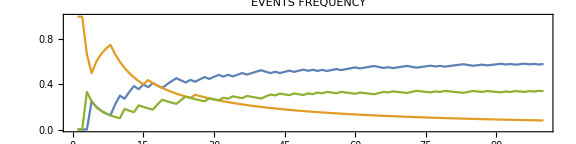

```mathematica
eventsCum=Table[Total[Take[events,t]/(t-1),{1}],{t,2,Dimensions[events]⟦1⟧}];
eventsPlot=Show[
ListPlot[Flatten[Table[eventsCum⟦All,i,j⟧,{i,wNegAll},{j,wPosAll}],{1,2}],
Joined->True,Frame->True,PlotRange->{{0,T},{0.0,1.0}},
PlotLegends->Flatten[Table[MaTeX["(-"<>ToString[i]<>","<>ToString[j]<>")"],{i,wNegAll},{j,wPosAll}],{1,2}],ImageSize->72 8],
AspectRatio->1/4,PlotLabel->"EVENTS FREQUENCY"
]
```

### Test case F (with visualizations)

```mathematica
<<MaTeX`
```

```mathematica
XNeg={{-1.0,0.0},{-1.0,1.0}};
XPos={{1.0,-1.0},{1.0,0.0},{1.0,2.0}};
X=Join[XNeg,XPos];
y={-1,-1,1,1,1};
{m,n}=Dimensions[X];
mNeg=Length[XNeg];
mPos=Length[XPos];
mins=Table[Min[X⟦All,k⟧],{k,1,Dimensions[X]⟦2⟧}];
maxs=Table[Max[X⟦All,k⟧],{k,1,Dimensions[X]⟦2⟧}];
```

```mathematica
Xy=Transpose[Join[Transpose[X],{y}]];
Export[NotebookDirectory[]<>"../data/testcase_f.txt",Xy,"Table"]
```

C:\iis\Articles\paper_50_boosted_random_planes\mathematica\../data/testcase_f.txt

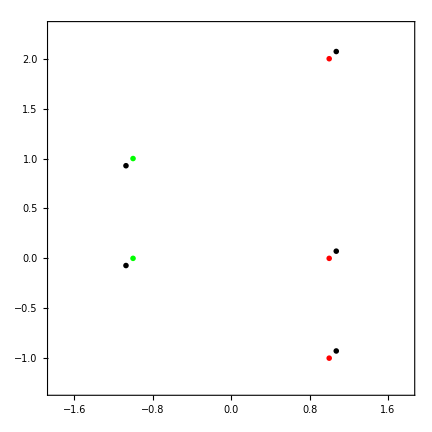

```mathematica
range=1.2Max[Table[maxs⟦i⟧-mins⟦i⟧,{i,1,Dimensions[X]⟦2⟧}]];
labelShift=0.02range;
plotRange=Table[{0.5(maxs⟦i⟧+mins⟦i⟧)-0.5range,0.5(maxs⟦i⟧+mins⟦i⟧)+0.5range},{i,1,Dimensions[X]⟦2⟧}];
dataPlot=Show[
ListPlot[{XNeg,XPos},PlotStyle->{{AbsolutePointSize[4],Green},{AbsolutePointSize[4],Red}},Frame->True,Axes->False,AspectRatio->1,
ImageSize->72 6,PlotRange->plotRange],
Graphics[Table[Text[MaTeX["\\mathbf{x}_{-"<>ToString[i]<>"}"],XNeg⟦i⟧-labelShift],{i,1,mNeg}]],
Graphics[Table[Text[MaTeX["\\mathbf{x}_{"<>ToString[j]<>"}"],XPos⟦j⟧+labelShift],{j,1,mPos}]]
]
```

```mathematica
AbsoluteTiming[brpResult=BoostedRandomPlanes[X,y,0,1000]]
```

BOOSTED RANDOM PLANES...

BOOSTED RANDOM PLANES DONE.

{0.00156955,{-0.000536632,0.999999,0.00111915}}

```mathematica
brpV=brpResult⟦Range[2,Length[brpResult]]⟧;
brpV0=brpResult⟦1⟧;
brpτ=Margin[X,y,brpV,brpV0]
```

0.998344

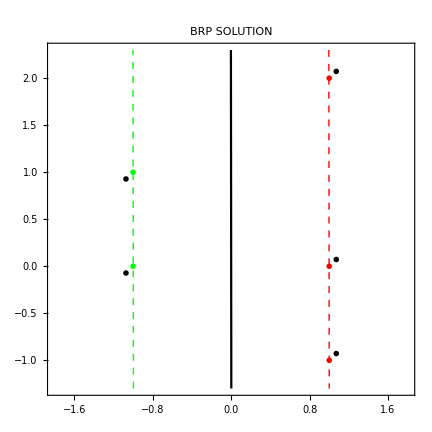

```mathematica
brpPlot=ContourPlot[{brpV0+brpV.{x1,x2}==0.0,brpV0+brpV.{x1,x2}==-brpτ,brpV0+brpV.{x1,x2}==brpτ},
{x1,plotRange⟦1,1⟧,plotRange⟦1,2⟧},{x2,plotRange⟦2,1⟧,plotRange⟦2,2⟧},ContourStyle->{Black,{Dashed,Thin,Green},{Dashed,Thin,Red}}
];
brpPlotAll=Show[brpPlot,dataPlot,ImageSize->72 6,PlotLabel->"BRP SOLUTION"]
```

```mathematica
T=100;
{brpVInfo,brpV0Info,wNegHistory,wPosHistory,events,solutionHistory}=BoostedRandomPlanesInformative[X,y,0,T];
```

BOOSTED RANDOM PLANES INFORMATIVE...

BOOSTED RANDOM PLANES INFORMATIVE DONE.

```mathematica
suppRatio=-1.0;
eventsTotal=Total[events,{1}]/T;
eventsSupp=Position[eventsTotal,x_/;x>suppRatio];
wNegAll=Union[eventsSupp⟦All,1⟧];
wPosAll=Union[eventsSupp⟦All,2⟧];
```

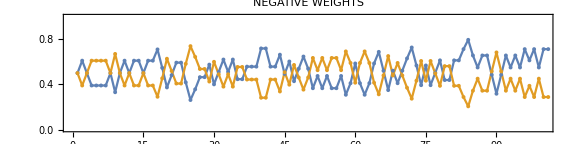

```mathematica
wNegPlot=Show[
ListPlot[Transpose[wNegHistory⟦All,wNegAll⟧],
Joined->True,Frame->True,PlotRange->{{0,T},{0.0,1.0}},ImageSize->72 8,PlotMarkers->Graphics[{Disk[]},ImageSize->4],PlotLegends->Map[MaTeX["\\mathbf{x}_{-"<>ToString[#]<>"}"]&,wNegAll]
],
AspectRatio->1/4,PlotLabel->"NEGATIVE WEIGHTS"
]
```

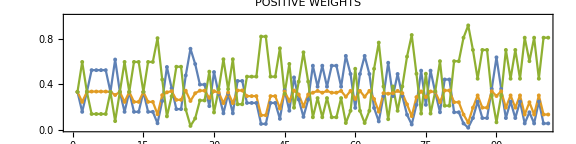

```mathematica
wPosPlot=Show[
ListPlot[Transpose[wPosHistory⟦All,wPosAll⟧],
Joined->True,Frame->True,PlotRange->{{0,T},{0.0,1.0}},ImageSize->72 8,PlotMarkers->Graphics[{Disk[]},ImageSize->4],PlotLegends->Map[MaTeX["\\mathbf{x}_{"<>ToString[#]<>"}"]&,wPosAll]
],
AspectRatio->1/4,PlotLabel->"POSITIVE WEIGHTS"
]
```

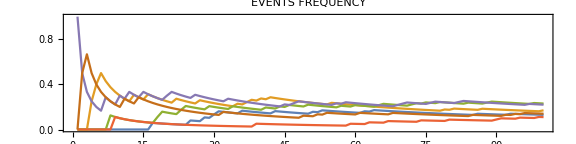

```mathematica
eventsCum=Table[Total[Take[events,t]/(t-1),{1}],{t,2,Dimensions[events]⟦1⟧}];
eventsPlot=Show[
ListPlot[Flatten[Table[eventsCum⟦All,i,j⟧,{i,wNegAll},{j,wPosAll}],{1,2}],
Joined->True,Frame->True,PlotRange->{{0,T},{0.0,1.0}},
PlotLegends->Flatten[Table[MaTeX["(-"<>ToString[i]<>","<>ToString[j]<>")"],{i,wNegAll},{j,wPosAll}],{1,2}],ImageSize->72 8],
AspectRatio->1/4,PlotLabel->"EVENTS FREQUENCY"
]
```

### Test case G (with visualizations)

```mathematica
<<MaTeX`
```

```mathematica
XNeg={{-1.0,-1.0},{-1.0,0.0}};
XPos={{1.0,0.0},{1.0,1.0},{1.0,2.0},{1.0,3.0},{1.0,4.0}};
X=Join[XNeg,XPos];
y={-1,-1,1,1,1,1,1};
{m,n}=Dimensions[X];
mNeg=Length[XNeg];
mPos=Length[XPos];
mins=Table[Min[X⟦All,k⟧],{k,1,Dimensions[X]⟦2⟧}];
maxs=Table[Max[X⟦All,k⟧],{k,1,Dimensions[X]⟦2⟧}];
```

```mathematica
Xy=Transpose[Join[Transpose[X],{y}]];
Export[NotebookDirectory[]<>"../data/testcase_g.txt",Xy,"Table"]
```

C:\iis\Articles\paper_50_boosted_random_planes\mathematica\../data/testcase_g.txt

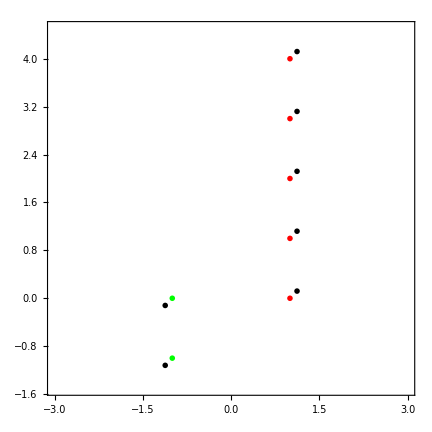

```mathematica
range=1.2Max[Table[maxs⟦i⟧-mins⟦i⟧,{i,1,Dimensions[X]⟦2⟧}]];
labelShift=0.02range;
plotRange=Table[{0.5(maxs⟦i⟧+mins⟦i⟧)-0.5range,0.5(maxs⟦i⟧+mins⟦i⟧)+0.5range},{i,1,Dimensions[X]⟦2⟧}];
dataPlot=Show[
ListPlot[{XNeg,XPos},PlotStyle->{{AbsolutePointSize[4],Green},{AbsolutePointSize[4],Red}},Frame->True,Axes->False,AspectRatio->1,
ImageSize->72 6,PlotRange->plotRange],
Graphics[Table[Text[MaTeX["\\mathbf{x}_{-"<>ToString[i]<>"}"],XNeg⟦i⟧-labelShift],{i,1,mNeg}]],
Graphics[Table[Text[MaTeX["\\mathbf{x}_{"<>ToString[j]<>"}"],XPos⟦j⟧+labelShift],{j,1,mPos}]]
]
```

```mathematica
AbsoluteTiming[brpResult=BoostedRandomPlanes[X,y,0,1000]]
```

BOOSTED RANDOM PLANES...

BOOSTED RANDOM PLANES DONE.

{0.00170302,{-0.0000211371,0.999975,0.00704569}}

```mathematica
brpV=brpResult⟦Range[2,Length[brpResult]]⟧;
brpV0=brpResult⟦1⟧;
brpτ=Margin[X,y,brpV,brpV0]
```

0.999954

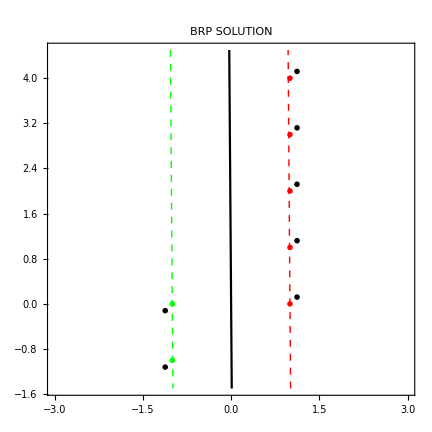

```mathematica
brpPlot=ContourPlot[{brpV0+brpV.{x1,x2}==0.0,brpV0+brpV.{x1,x2}==-brpτ,brpV0+brpV.{x1,x2}==brpτ},
{x1,plotRange⟦1,1⟧,plotRange⟦1,2⟧},{x2,plotRange⟦2,1⟧,plotRange⟦2,2⟧},ContourStyle->{Black,{Dashed,Thin,Green},{Dashed,Thin,Red}}
];
brpPlotAll=Show[brpPlot,dataPlot,ImageSize->72 6,PlotLabel->"BRP SOLUTION"]
```

```mathematica
T=100;
{brpVInfo,brpV0Info,wNegHistory,wPosHistory,events,solutionHistory}=BoostedRandomPlanesInformative[X,y,0,T];
```

BOOSTED RANDOM PLANES INFORMATIVE...

BOOSTED RANDOM PLANES INFORMATIVE DONE.

```mathematica
suppRatio=-1.0;
eventsTotal=Total[events,{1}]/T;
eventsSupp=Position[eventsTotal,x_/;x>suppRatio];
wNegAll=Union[eventsSupp⟦All,1⟧];
wPosAll=Union[eventsSupp⟦All,2⟧];
```

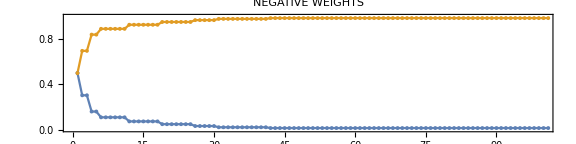

```mathematica
wNegPlot=Show[
ListPlot[Transpose[wNegHistory⟦All,wNegAll⟧],
Joined->True,Frame->True,PlotRange->{{0,T},{0.0,1.0}},ImageSize->72 8,PlotMarkers->Graphics[{Disk[]},ImageSize->4],PlotLegends->Map[MaTeX["\\mathbf{x}_{-"<>ToString[#]<>"}"]&,wNegAll]
],
AspectRatio->1/4,PlotLabel->"NEGATIVE WEIGHTS"
]
```

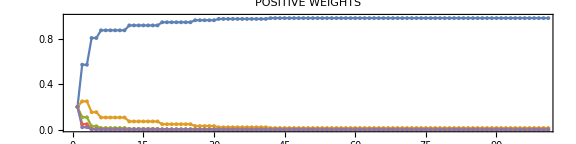

```mathematica
wPosPlot=Show[
ListPlot[Transpose[wPosHistory⟦All,wPosAll⟧],
Joined->True,Frame->True,PlotRange->{{0,T},{0.0,1.0}},ImageSize->72 8,PlotMarkers->Graphics[{Disk[]},ImageSize->4],PlotLegends->Map[MaTeX["\\mathbf{x}_{"<>ToString[#]<>"}"]&,wPosAll]
],
AspectRatio->1/4,PlotLabel->"POSITIVE WEIGHTS"
]
```

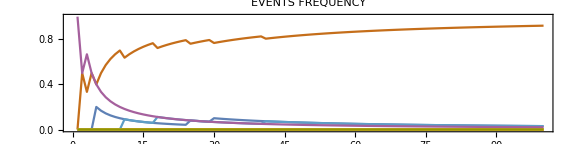

```mathematica
eventsCum=Table[Total[Take[events,t]/(t-1),{1}],{t,2,Dimensions[events]⟦1⟧}];
eventsPlot=Show[
ListPlot[Flatten[Table[eventsCum⟦All,i,j⟧,{i,wNegAll},{j,wPosAll}],{1,2}],Joined->True,Frame->True,PlotRange->{{0,T},{0.0,1.0}},PlotLegends->Flatten[Table[MaTeX["(-"<>ToString[i]<>","<>ToString[j]<>")"],{i,wNegAll},{j,wPosAll}],{1,2}],ImageSize->72 8],
AspectRatio->1/4,PlotLabel->"EVENTS FREQUENCY"
]
```

### Test case H (with visualizations)

```mathematica
<<MaTeX`
```

```mathematica
XNeg={{-1.0,-1.0},{-1.0,0.5}};
XPos={{1.0,0.0},{1.0,1.0},{1.0,2.0},{1.0,3.0},{1.0,4.0}};
X=Join[XNeg,XPos];
y={-1,-1,1,1,1,1,1};
{m,n}=Dimensions[X];
mNeg=Length[XNeg];
mPos=Length[XPos];
mins=Table[Min[X⟦All,k⟧],{k,1,Dimensions[X]⟦2⟧}];
maxs=Table[Max[X⟦All,k⟧],{k,1,Dimensions[X]⟦2⟧}];
```

```mathematica
Xy=Transpose[Join[Transpose[X],{y}]];
Export[NotebookDirectory[]<>"../data/testcase_h.txt",Xy,"Table"]
```

C:\iis\Articles\paper_50_boosted_random_planes\mathematica\../data/testcase_h.txt

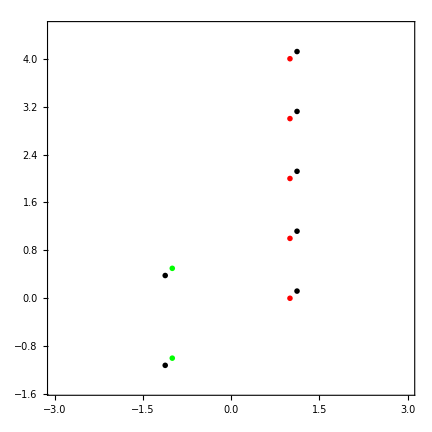

```mathematica
range=1.2Max[Table[maxs⟦i⟧-mins⟦i⟧,{i,1,Dimensions[X]⟦2⟧}]];
labelShift=0.02range;
plotRange=Table[{0.5(maxs⟦i⟧+mins⟦i⟧)-0.5range,0.5(maxs⟦i⟧+mins⟦i⟧)+0.5range},{i,1,Dimensions[X]⟦2⟧}];
dataPlot=Show[
ListPlot[{XNeg,XPos},PlotStyle->{{AbsolutePointSize[4],Green},{AbsolutePointSize[4],Red}},Frame->True,Axes->False,AspectRatio->1,
ImageSize->72 6,PlotRange->plotRange],
Graphics[Table[Text[MaTeX["\\mathbf{x}_{-"<>ToString[i]<>"}"],XNeg⟦i⟧-labelShift],{i,1,mNeg}]],
Graphics[Table[Text[MaTeX["\\mathbf{x}_{"<>ToString[j]<>"}"],XPos⟦j⟧+labelShift],{j,1,mPos}]]
]
```

```mathematica
AbsoluteTiming[brpResult=BoostedRandomPlanes[X,y,0,1000]]
```

BOOSTED RANDOM PLANES...

BOOSTED RANDOM PLANES DONE.

{0.00192766,{-0.000540987,0.999999,0.00169059}}

```mathematica
brpV=brpResult⟦Range[2,Length[brpResult]]⟧;
brpV0=brpResult⟦1⟧;
brpτ=Margin[X,y,brpV,brpV0]
```

0.999458

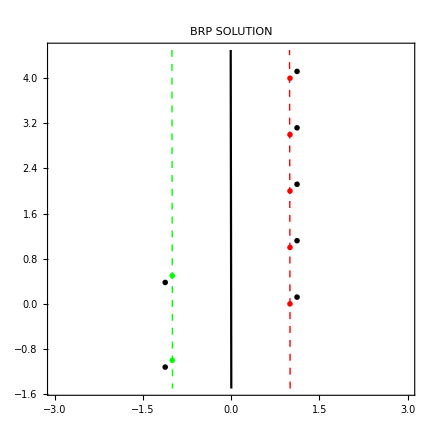

```mathematica
brpPlot=ContourPlot[{brpV0+brpV.{x1,x2}==0.0,brpV0+brpV.{x1,x2}==-brpτ,brpV0+brpV.{x1,x2}==brpτ},
{x1,plotRange⟦1,1⟧,plotRange⟦1,2⟧},{x2,plotRange⟦2,1⟧,plotRange⟦2,2⟧},ContourStyle->{Black,{Dashed,Thin,Green},{Dashed,Thin,Red}}
];
brpPlotAll=Show[brpPlot,dataPlot,ImageSize->72 6,PlotLabel->"BRP SOLUTION"]
```

```mathematica
T=100;
{brpVInfo,brpV0Info,wNegHistory,wPosHistory,events,solutionHistory}=BoostedRandomPlanesInformative[X,y,0,T];
```

BOOSTED RANDOM PLANES INFORMATIVE...

BOOSTED RANDOM PLANES INFORMATIVE DONE.

```mathematica
suppRatio=-1.0;
eventsTotal=Total[events,{1}]/T;
eventsSupp=Position[eventsTotal,x_/;x>suppRatio];
wNegAll=Union[eventsSupp⟦All,1⟧];
wPosAll=Union[eventsSupp⟦All,2⟧];
```

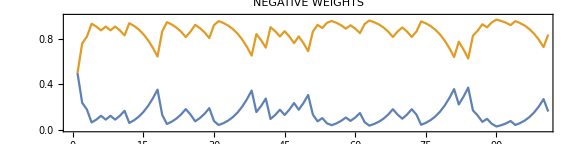

```mathematica
wNegPlot=Show[
ListPlot[Transpose[wNegHistory⟦All,wNegAll⟧],
Joined->True,Frame->True,PlotRange->{{0,T},{0.0,1.0}},ImageSize->72 8,PlotLegends->Map[MaTeX["\\mathbf{x}_{-"<>ToString[#]<>"}"]&,wNegAll]
],
AspectRatio->1/4,PlotLabel->"NEGATIVE WEIGHTS"
]
```

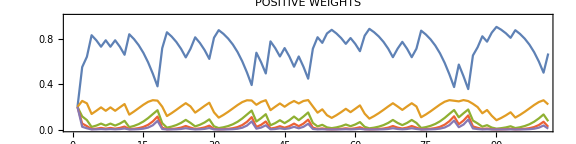

```mathematica
wPosPlot=Show[
ListPlot[Transpose[wPosHistory⟦All,wPosAll⟧],
Joined->True,Frame->True,PlotRange->{{0,T},{0.0,1.0}},ImageSize->72 8,PlotLegends->Map[MaTeX["\\mathbf{x}_{"<>ToString[#]<>"}"]&,wPosAll]
],
AspectRatio->1/4,PlotLabel->"POSITIVE WEIGHTS"
]
```

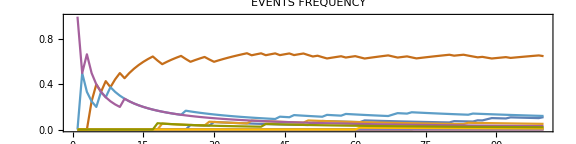

```mathematica
eventsCum=Table[Total[Take[events,t]/(t-1),{1}],{t,2,Dimensions[events]⟦1⟧}];
events=Show[
ListPlot[Flatten[Table[eventsCum⟦All,i,j⟧,{i,wNegAll},{j,wPosAll}],{1,2}],Joined->True,Frame->True,PlotRange->{{0,T},{0.0,1.0}},PlotLegends->Flatten[Table[MaTeX["(-"<>ToString[i]<>","<>ToString[j]<>")"],{i,wNegAll},{j,wPosAll}],{1,2}],ImageSize->72 8],
AspectRatio->1/4,PlotLabel->"EVENTS FREQUENCY"
]
```

### Normals 2D 10k

```mathematica
SeedRandom[0];
m=10000;
mNeg=0.5 m;
mPos=0.5 m;
XNeg=RandomVariate[MultinormalDistribution[1.0{-1,-1},0.5{{2.0,-3.0},{-3.0,5.0}}],mNeg];
XPos=RandomVariate[MultinormalDistribution[1.0{1,1},0.5{{2.0,-3.0},{-3.0,5.0}}],mPos];
X=Join[XNeg,XPos];
{m,n}=Dimensions[X];
y=Table[-1,m];
y⟦Range[mPos+1,m]⟧=1;
mins=Table[Min[X⟦All,k⟧],{k,1,Dimensions[X]⟦2⟧}];
maxs=Table[Max[X⟦All,k⟧],{k,1,Dimensions[X]⟦2⟧}];
```

```mathematica
Xy=Transpose[Join[Transpose[X],{y}]];
Export[NotebookDirectory[]<>"../data/normals2d_10k.txt",Xy,"Table"]
```

C:\iis\Articles\paper_50_boosted_random_planes\mathematica\../data/normals2d_10k.txt

```mathematica
AbsoluteTiming[brpResult=BoostedRandomPlanes[X,y,0,100]]
```

BOOSTED RANDOM PLANES...

BOOSTED RANDOM PLANES DONE.

{0.0129789,{-0.0126879,0.852935,0.522017}}

```mathematica
brpV=brpResult⟦Range[2,Length[brpResult]]⟧;
brpV0=brpResult⟦1⟧;
brpτ=Margin[X,y,brpV,brpV0]
```

0.43576

```mathematica
AbsoluteTiming[brpfResult=BoostedRandomPlanesFast[X,y,0,1000,100,0.05]]
```

BOOSTED RANDOM PLANES FAST...

[TRIMMING DOWN TO {3, 3} SUPPORT VECTORS.]

BOOSTED RANDOM PLANES FAST DONE.

{0.0110892,{0.00834082,0.845492,0.533988}}

```mathematica
brpfV=brpfResult⟦Range[2,Length[brpfResult]]⟧;
brpfV0=brpfResult⟦1⟧;
brpfτ=Margin[X,y,brpfV,brpfV0]
```

0.504895

### Normals 3D 10k

```mathematica
SeedRandom[0];
m=10000;
mNeg=0.5 m;
mPos=0.5 m;
XNeg=RandomVariate[MultinormalDistribution[{-1.0,0,0},0.05{{1.0,0.0,0.0},{0.0,10.0,0.0},{0.0,0.0,10.0}}],mNeg];
XPos=RandomVariate[MultinormalDistribution[{1.0,0,0},0.05{{1.0,0.0,0.0},{0.0,10.0,0.0},{0.0,0.0,10.0}}],mPos];
X=Join[XNeg,XPos];
{m,n}=Dimensions[X];
y=Table[-1,m];
y⟦Range[mPos+1,m]⟧=1;
mins=Table[Min[X⟦All,k⟧],{k,1,Dimensions[X]⟦2⟧}];
maxs=Table[Max[X⟦All,k⟧],{k,1,Dimensions[X]⟦2⟧}];
```

```mathematica
Xy=Transpose[Join[Transpose[X],{y}]];
Export[NotebookDirectory[]<>"../data/normals3d_10k.txt",Xy,"Table"]
```

C:\iis\Articles\paper_50_boosted_random_planes\mathematica\../data/normals3d_10k.txt

```mathematica
AbsoluteTiming[brpResult=BoostedRandomPlanes[X,y,0,100]]
```

BOOSTED RANDOM PLANES...

BOOSTED RANDOM PLANES DONE.

{0.0109487,{-0.0655027,0.999156,-0.034563,-0.0221832}}

```mathematica
brpV=brpResult⟦Range[2,Length[brpResult]]⟧;
brpV0=brpResult⟦1⟧;
brpτ=Margin[X,y,brpV,brpV0]
```

0.128989

```mathematica
AbsoluteTiming[brpfResult=BoostedRandomPlanesFast[X,y,0,1000,100,0.05]]
```

BOOSTED RANDOM PLANES FAST...

[TRIMMING DOWN TO {2, 3} SUPPORT VECTORS.]

BOOSTED RANDOM PLANES FAST DONE.

{0.0115539,{-0.0284737,0.996694,-0.0769299,-0.0261502}}

```mathematica
brpfV=brpfResult⟦Range[2,Length[brpfResult]]⟧;
brpfV0=brpfResult⟦1⟧;
brpfτ=Margin[X,y,brpfV,brpfV0]
```

0.160239

### Normals 2D 100k

```mathematica
SeedRandom[0];
m=100000;
mNeg=0.5 m;
mPos=0.5 m;
XNeg=RandomVariate[MultinormalDistribution[1.0{-1.0,0.0},0.05{{1.0,0.0},{0.0,100.0}}],mNeg];
XPos=RandomVariate[MultinormalDistribution[1.0{1.0,0.0},0.05{{1.0,0.0},{0.0,100.0}}],mPos];
X=Join[XNeg,XPos];
{m,n}=Dimensions[X];
y=Table[-1,m];
y⟦Range[mPos+1,m]⟧=1;
mins=Table[Min[X⟦All,k⟧],{k,1,Dimensions[X]⟦2⟧}];
maxs=Table[Max[X⟦All,k⟧],{k,1,Dimensions[X]⟦2⟧}];
```

```mathematica
Xy=Transpose[Join[Transpose[X],{y}]];
Export[NotebookDirectory[]<>"../data/normals2d_100k.txt",Xy,"Table"]
```

C:\iis\Articles\paper_50_boosted_random_planes\mathematica\../data/normals2d_100k.txt

```mathematica
AbsoluteTiming[brpResult=BoostedRandomPlanes[X,y,0,100]]
```

BOOSTED RANDOM PLANES...

BOOSTED RANDOM PLANES DONE.

{0.0861979,{0.0191205,0.996622,-0.0821314}}

```mathematica
brpV=brpResult⟦Range[2,Length[brpResult]]⟧;
brpV0=brpResult⟦1⟧;
brpτ=Margin[X,y,brpV,brpV0]
```

-0.289402

```mathematica
AbsoluteTiming[brpfResult=BoostedRandomPlanesFast[X,y,0,1000,100,0.05]]
```

BOOSTED RANDOM PLANES FAST...

[TRIMMING DOWN TO {2, 4} SUPPORT VECTORS.]

BOOSTED RANDOM PLANES FAST DONE.

{0.0771598,{0.0143118,0.99994,-0.0109916}}

```mathematica
brpfV=brpfResult⟦Range[2,Length[brpfResult]]⟧;
brpfV0=brpfResult⟦1⟧;
brpfτ=Margin[X,y,brpfV,brpfV0]
```

-0.00255009

### Normals 3D 100k

```mathematica
SeedRandom[0];
m=100000;
mNeg=0.5 m;
mPos=0.5 m;
XNeg=RandomVariate[MultinormalDistribution[{-1.0,0,0},0.01{{1.0,0.0,0.0},{0.0,10.0,0.0},{0.0,0.0,10.0}}],mNeg];
XPos=RandomVariate[MultinormalDistribution[{1.0,0,0},0.01{{1.0,0.0,0.0},{0.0,10.0,0.0},{0.0,0.0,10.0}}],mPos];
X=Join[XNeg,XPos];
{m,n}=Dimensions[X];
y=Table[-1,m];
y⟦Range[mPos+1,m]⟧=1;
mins=Table[Min[X⟦All,k⟧],{k,1,Dimensions[X]⟦2⟧}];
maxs=Table[Max[X⟦All,k⟧],{k,1,Dimensions[X]⟦2⟧}];
```

```mathematica
Xy=Transpose[Join[Transpose[X],{y}]];
Export[NotebookDirectory[]<>"../data/normals3d_100k.txt",Xy,"Table"]
```

C:\iis\Articles\paper_50_boosted_random_planes\mathematica\../data/normals3d_100k.txt

```mathematica
AbsoluteTiming[brpResult=BoostedRandomPlanes[X,y,0,100]]
```

BOOSTED RANDOM PLANES...

BOOSTED RANDOM PLANES DONE.

{0.0855224,{0.0000592672,0.998963,-0.00870763,-0.0446884}}

```mathematica
brpV=brpResult⟦Range[2,Length[brpResult]]⟧;
brpV0=brpResult⟦1⟧;
brpτ=Margin[X,y,brpV,brpV0]
```

0.564118

```mathematica
AbsoluteTiming[brpfResult=BoostedRandomPlanesFast[X,y,0,1000,100,0.05]]
```

BOOSTED RANDOM PLANES FAST...

[TRIMMING DOWN TO {2, 3} SUPPORT VECTORS.]

BOOSTED RANDOM PLANES FAST DONE.

{0.0915439,{-0.00319263,0.998726,-0.0207048,-0.0460111}}

```mathematica
brpfV=brpfResult⟦Range[2,Length[brpfResult]]⟧;
brpfV0=brpfResult⟦1⟧;
brpfτ=Margin[X,y,brpfV,brpfV0]
```

0.574421

### Iris

```mathematica
irisRawData=Import[NotebookDirectory[]<>"../data/iris.txt","Data"];
```

```mathematica
{m,n}=Dimensions[irisRawData];
n=n-1;
X=irisRawData⟦All,Range[n]⟧;
y=irisRawData⟦All,n+1⟧;
indexes=Union[Flatten[Position[y,"Iris-versicolor"]],Flatten[Position[y,"Iris-virginica"]]];
y=Table[-1,{m}];
y⟦indexes⟧=1;
mins=Table[Min[X⟦All,k⟧],{k,1,Dimensions[X]⟦2⟧}];
maxs=Table[Max[X⟦All,k⟧],{k,1,Dimensions[X]⟦2⟧}];
indNeg=Flatten[Position[y,-1]];
indPos=Flatten[Position[y,1]];
XNeg=X⟦indNeg⟧;
XPos=X⟦indPos⟧;
```

```mathematica
AbsoluteTiming[brpResult=BoostedRandomPlanes[X,y,0,100]]
```

BOOSTED RANDOM PLANES...

BOOSTED RANDOM PLANES DONE.

{0.0005422,{-1.37151,0.0728047,-0.422891,0.807262,0.405205}}

```mathematica
brpV=brpResult⟦Range[2,Length[brpResult]]⟧;
brpV0=brpResult⟦1⟧;
brpτ=Margin[X,y,brpV,brpV0]
```

0.810078

```mathematica
AbsoluteTiming[brpfResult=BoostedRandomPlanesFast[X,y,0,1000,100,0.05]]
```

BOOSTED RANDOM PLANES FAST...

[TRIMMING DOWN TO {3, 1} SUPPORT VECTORS.]

BOOSTED RANDOM PLANES FAST DONE.

{0.0019352,{-1.2024,0.0422235,-0.427956,0.817252,0.383627}}

```mathematica
brpfV=brpfResult⟦Range[2,Length[brpfResult]]⟧;
brpfV0=brpfResult⟦1⟧;
brpfτ=Margin[X,y,brpfV,brpfV0]
```

0.816791

```mathematica
TimeConstrained[AbsoluteTiming[svmResult=SVM[X,y]],60]
```

{6.20793,{-1.45058,0.0460404,-0.521725,1.00316,0.464186}}

```mathematica
svmV=Take[svmResult,-n];
svmV0=svmResult⟦1⟧;
svmτ=Margin[X,y,svmV,svmV0]
```

0.817556

```mathematica
CompareSolutions[brpV,brpV0,svmV,svmV0,X,y]
```

BRP VS SVM COMPARISON OF SOLUTIONS...

NORM OF DIFFERENCE: 0.000091152

RATIO OF MARGINS: 0.99999

{0.000091152,0.99999}

```mathematica
TimeConstrained[AbsoluteTiming[svmdResult=SVMDual[X,y,0.0]],60]
```

$Aborted

### Sonar

```mathematica
sonarRawData=Import[NotebookDirectory[]<>"../data/sonar.all-data","Data"];
```

```mathematica
{m,n}=Dimensions[sonarRawData];
n=n-1;
X=sonarRawData⟦All,Range[1,n]⟧;
y=sonarRawData⟦All,n+1⟧;
indexes=Flatten[Position[y,"R"]];
y=Table[1,{m}];
y⟦indexes⟧=-1;
```

```mathematica
AbsoluteTiming[brpResult=BoostedRandomPlanes[X,y,0,100]]
```

BOOSTED RANDOM PLANES...

BOOSTED RANDOM PLANES DONE.

{0.0009347,{-0.273401,0.0860448,0.100398,0.0555364,0.128932,0.0785321,-0.0668194,-0.140861,-0.151904,0.185507,0.158952,0.216095,-0.0165901,0.0628937,-0.0779217,-0.0521263,-0.0577812,0.00533452,-0.0273225,0.0277617,0.107361,0.0578925,0.0972683,0.057443,-0.0214234,-0.163966,-0.00876845,0.0804801,0.0357609,0.112152,0.0117506,-0.358613,0.0395546,0.0836896,-0.106441,-0.156249,-0.171451,-0.131477,0.161523,0.205867,-0.10901,-0.0413101,0.0939927,0.124606,0.2178,0.373174,0.275831,0.203232,0.23298,0.142302,0.0177023,0.0409102,0.0371217,0.011417,0.014557,-0.015935,-0.000200939,-0.021094,0.0201137,0.00237995,-0.00144435}}

```mathematica
brpV=brpResult⟦Range[2,Length[brpResult]]⟧;
brpV0=brpResult⟦1⟧;
brpτ=Margin[X,y,brpV,brpV0]
```

-0.258508

```mathematica
AbsoluteTiming[brpfResult=BoostedRandomPlanesFast[X,y,0, 1000000,1000,0.05]]
```

BOOSTED RANDOM PLANES FAST...

[TRIMMING RATIO TOO LARGE FOR POSITIVE CLASS, TAKING ALL INDEXES.]

[TRIMMING DOWN TO {3, 111} SUPPORT VECTORS.]

BOOSTED RANDOM PLANES FAST DONE.

{4.15196,{0.301557,0.0537728,0.039246,-0.0594231,-0.0753109,-0.124104,-0.0658652,-0.0787682,-0.0964006,-0.148493,-0.190085,-0.0652472,-0.177579,0.0494876,0.0457145,-0.0579646,0.0149692,0.0411166,0.280415,-0.169397,-0.16023,-0.0362146,0.0672168,0.0194031,-0.0402211,-0.0660598,0.136104,-0.134083,-0.12412,0.407705,0.0847531,-0.175292,0.214801,0.244337,-0.00366904,0.0349837,0.327013,0.00640807,-0.285416,-0.202351,-0.0629102,-0.128412,0.134753,0.0895644,0.152603,0.080488,0.0382659,0.00291718,0.13802,0.0938545,0.019263,0.0389158,0.0160218,0.0106037,0.0215716,0.00234301,-0.00480326,-0.0315721,0.00801945,0.00702116,0.00786047}}

```mathematica
brpfV=brpfResult⟦Range[2,Length[brpfResult]]⟧;
brpfV0=brpfResult⟦1⟧;
brpfτ=Margin[X,y,brpfV,brpfV0]
```

-1.00561

```mathematica
TimeConstrained[AbsoluteTiming[svmResult=SVM[X,y]],60]
```

$Aborted

### Leukemia

```mathematica
leukemiaRawData=Import[NotebookDirectory[]<>"../data/leukemia_big.csv","Data"];
```

```mathematica
{n,m}=Dimensions[leukemiaRawData];(* originally transposed data *)
n=n-1;
tempY=leukemiaRawData⟦1⟧;
leukemiaRawData=leukemiaRawData⟦Range[2,n+1],All⟧;
leukemiaRawData=Transpose[Join[leukemiaRawData,{tempY}]];
X=leukemiaRawData⟦All,Range[1,n]⟧;
y=leukemiaRawData⟦All,n+1⟧;
indexes=Flatten[Position[y,"ALL"]];
y=Table[1,{m}];
y⟦indexes⟧=-1;
```

```mathematica
AbsoluteTiming[brpResult=BoostedRandomPlanes[X,y,0,100];]
```

BOOSTED RANDOM PLANES...

BOOSTED RANDOM PLANES DONE.

{0.0259168,Null}

```mathematica
brpV=brpResult⟦Range[2,Length[brpResult]]⟧;
brpV0=brpResult⟦1⟧;
brpτ=Margin[X,y,brpV,brpV0]
```

6.99196

```mathematica
AbsoluteTiming[brpfResult=BoostedRandomPlanesFast[X,y,0, 1000,100,0.05];]
```

BOOSTED RANDOM PLANES FAST...

[TRIMMING DOWN TO {7, 7} SUPPORT VECTORS.]

BOOSTED RANDOM PLANES FAST DONE.

{0.125491,Null}

```mathematica
brpfV=brpfResult⟦Range[2,Length[brpfResult]]⟧;
brpfV0=brpfResult⟦1⟧;
brpfτ=Margin[X,y,brpfV,brpfV0]
```

-1.11535

```mathematica
TimeConstrained[AbsoluteTiming[svmResult=SVM[X,y]],60]
```

$Aborted

### Moons (non linear, with visualization)

```mathematica
<<MaTeX`
```

```mathematica
moonsRawData=Import[NotebookDirectory[]<>"../data/moons.txt","Data"];
```

```mathematica
{m,n}=Dimensions[moonsRawData];
n=n-1;
X=moonsRawData⟦All,Range[n]⟧;
y=moonsRawData⟦All,n+1⟧;
indexes=Flatten[Position[y,0.0]];
y=Table[1,{m}];
y⟦indexes⟧=-1;
mins=Table[Min[X⟦All,k⟧],{k,1,Dimensions[X]⟦2⟧}];
maxs=Table[Max[X⟦All,k⟧],{k,1,Dimensions[X]⟦2⟧}];
indNeg=Flatten[Position[y,-1]];
indPos=Flatten[Position[y,1]];
XNeg=X⟦indNeg⟧;
XPos=X⟦indPos⟧;
```

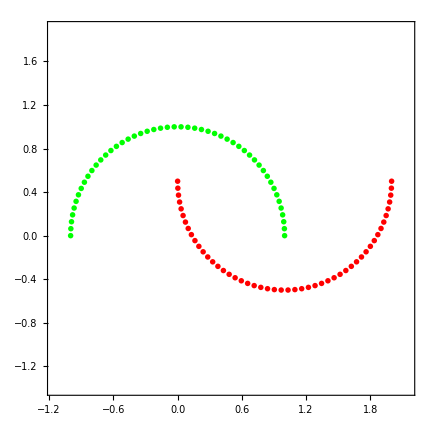

```mathematica
range=1.1Max[Table[maxs⟦i⟧-mins⟦i⟧,{i,1,Dimensions[X]⟦2⟧}]];
labelShift=0.02range;
plotRange=Table[{0.5(maxs⟦i⟧+mins⟦i⟧)-0.5range,0.5(maxs⟦i⟧+mins⟦i⟧)+0.5range},{i,1,Dimensions[X]⟦2⟧}];
dataPlot=Show[
ListPlot[{XNeg,XPos},PlotStyle->{{Green},{Red}},Frame->True,Axes->False,AspectRatio->1,
ImageSize->72 6,PlotRange->plotRange]
]
```

```mathematica
Ts={1,2,3,5,10,20,50,100};
```

```mathematica
AbsoluteTiming[brpnls=Table[BoostedRandomPlanesLogits[X,y,0,T ],{T,Ts}]];
```

BOOSTED RANDOM PLANES LOGITS...

BOOSTED RANDOM PLANES LOGITS DONE.

BOOSTED RANDOM PLANES LOGITS...

BOOSTED RANDOM PLANES LOGITS DONE.

BOOSTED RANDOM PLANES LOGITS...

BOOSTED RANDOM PLANES LOGITS DONE.

BOOSTED RANDOM PLANES LOGITS...

BOOSTED RANDOM PLANES LOGITS DONE.

BOOSTED RANDOM PLANES LOGITS...

BOOSTED RANDOM PLANES LOGITS DONE.

BOOSTED RANDOM PLANES LOGITS...

BOOSTED RANDOM PLANES LOGITS DONE.

BOOSTED RANDOM PLANES LOGITS...

BOOSTED RANDOM PLANES LOGITS DONE.

BOOSTED RANDOM PLANES LOGITS...

BOOSTED RANDOM PLANES LOGITS DONE.

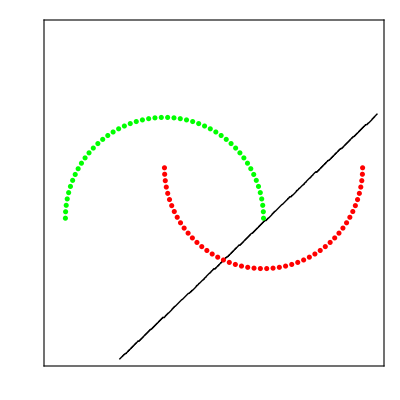
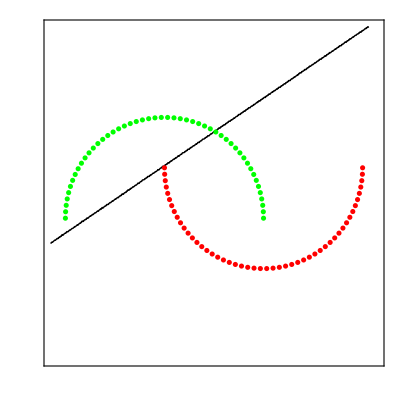
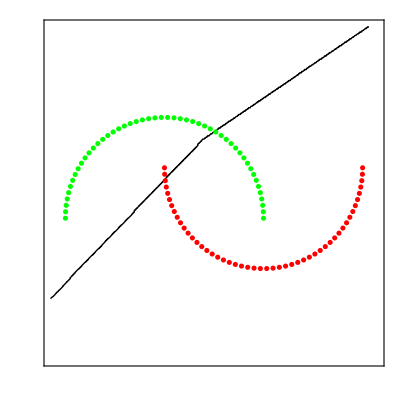
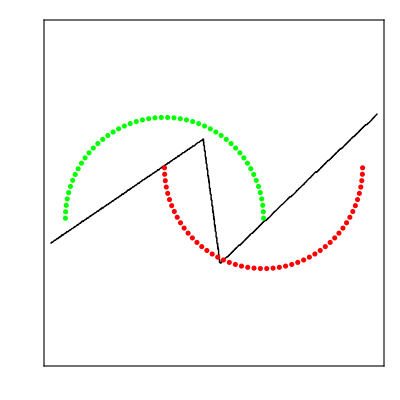
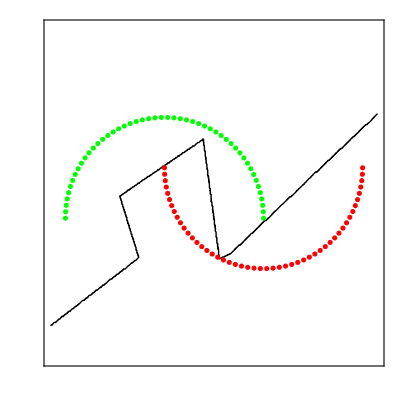
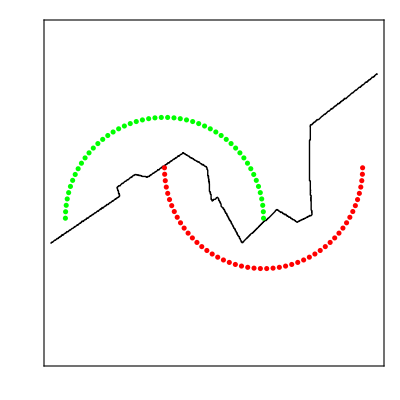
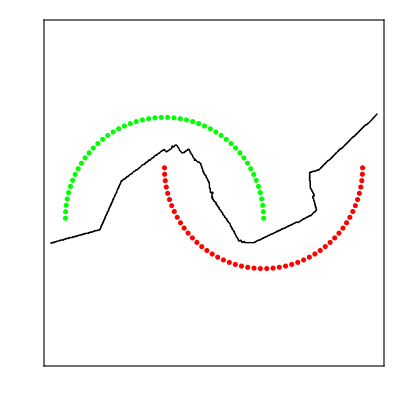
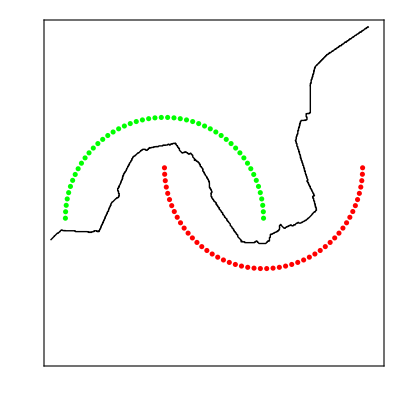

```mathematica
brpnlPlots=Table[
Show[
ContourPlot[BoostedRandomPlanesLogitsClassify[{x1,x2},brpnls⟦k⟧],
{x1,plotRange⟦1,1⟧,plotRange⟦1,2⟧},{x2,plotRange⟦2,1⟧,plotRange⟦2,2⟧},PlotPoints->50,ContourShading->None,ContourStyle->{Black},Contours->1],dataPlot,
PlotLabel->MaTeX["T="<>ToString[Ts⟦k⟧]],FrameTicks->None],
{k,1,Length[Ts]}]
```

### Chessboard (non linear, with visualization)

```mathematica
<<MaTeX`
```

```mathematica
SeedRandom[0];
m=1000;
chessboardN=3;
X=Table[RandomReal[] chessboardN,{m},{2}];
y=Table[Mod[Total[Map[Floor[#]&,X⟦i⟧]],2],{i,1,m}];
indexes=Flatten[Position[y,0]];
y=Table[1,{m}];
y⟦indexes⟧=-1;
mins=Table[Min[X⟦All,k⟧],{k,1,Dimensions[X]⟦2⟧}];
maxs=Table[Max[X⟦All,k⟧],{k,1,Dimensions[X]⟦2⟧}];
indNeg=Flatten[Position[y,-1]];
indPos=Flatten[Position[y,1]];
XNeg=X⟦indNeg⟧;
XPos=X⟦indPos⟧;
```

```mathematica
Xy=Transpose[Join[Transpose[X],{y}]];
Export[NotebookDirectory[]<>"../data/chessboard.txt",Xy,"Table"]
```

C:\iis\Articles\paper_50_boosted_random_planes\mathematica\../data/chessboard.txt

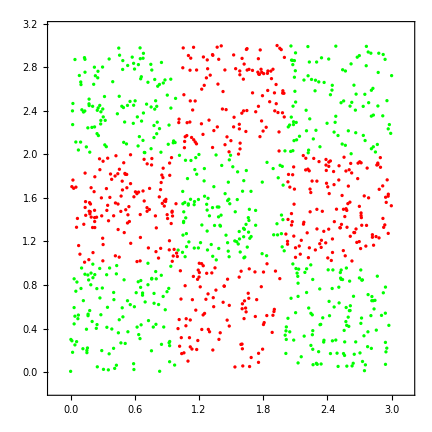

```mathematica
range=1.1Max[Table[maxs⟦i⟧-mins⟦i⟧,{i,1,Dimensions[X]⟦2⟧}]];
labelShift=0.02range;
plotRange=Table[{0.5(maxs⟦i⟧+mins⟦i⟧)-0.5range,0.5(maxs⟦i⟧+mins⟦i⟧)+0.5range},{i,1,Dimensions[X]⟦2⟧}];
dataPlot=Show[
ListPlot[{XNeg,XPos},PlotStyle->{{Green},{Red}},Frame->True,Axes->False,AspectRatio->1,
ImageSize->72 6,PlotRange->plotRange]
]
```

```mathematica
Ts={50,100,200,500};
```

```mathematica
AbsoluteTiming[brpnls=Table[BoostedRandomPlanesLogits[X,y,0,T ],{T,Ts}]];
```

BOOSTED RANDOM PLANES LOGITS...

BOOSTED RANDOM PLANES LOGITS DONE.

BOOSTED RANDOM PLANES LOGITS...

BOOSTED RANDOM PLANES LOGITS DONE.

BOOSTED RANDOM PLANES LOGITS...

BOOSTED RANDOM PLANES LOGITS DONE.

BOOSTED RANDOM PLANES LOGITS...

BOOSTED RANDOM PLANES LOGITS DONE.

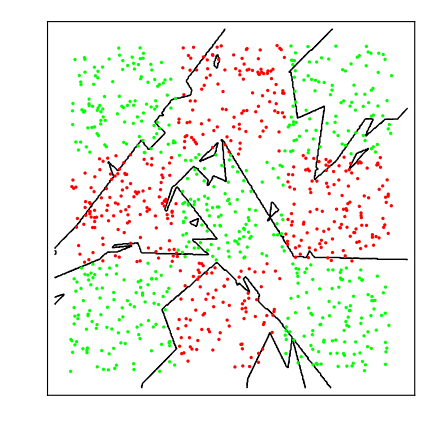
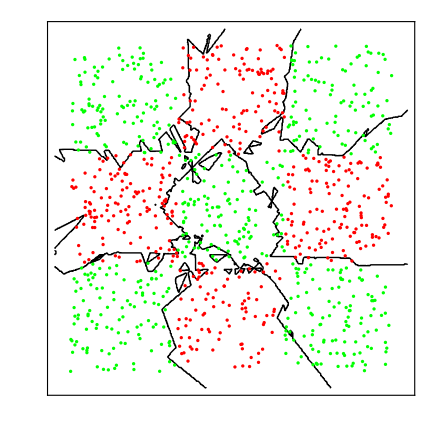
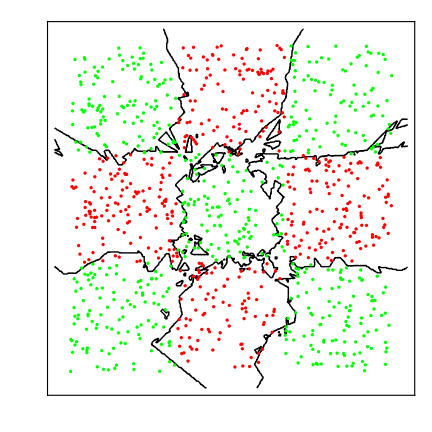
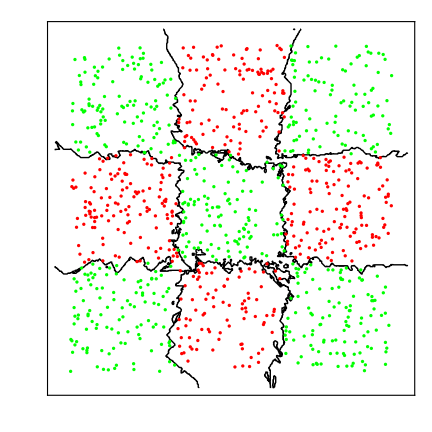

```mathematica
brpnlPlots=Table[
Show[
ContourPlot[BoostedRandomPlanesLogitsClassify[{x1,x2},brpnls⟦k⟧],
{x1,plotRange⟦1,1⟧,plotRange⟦1,2⟧},{x2,plotRange⟦2,1⟧,plotRange⟦2,2⟧},PlotPoints->50,ContourShading->None,ContourStyle->{Black},Contours->1,ImageSize->72 6],
dataPlot,
PlotLabel->MaTeX["T="<>ToString[Ts⟦k⟧]],FrameTicks->None],
{k,1,Length[Ts]}]
```

### Ionosphere (non linear)

```mathematica
ionosphereRawData=Import[NotebookDirectory[]<>"../data/ionosphere.data","Data"];
```

```mathematica
{m,n}=Dimensions[ionosphereRawData];
n=n-1;
X=ionosphereRawData⟦All,Range[1,n]⟧;
y=ionosphereRawData⟦All,n+1⟧;
indexes=Flatten[Position[y,"g"]];
y=Table[1,{m}];
y⟦indexes⟧=-1;
```

```mathematica
SeedRandom[0];
mTrain=Round[0.8 m];
mTest=m-mTrain;
trainIndexes=RandomSample[Range[m],mTrain];
testIndexes=Complement[Range[m],trainIndexes];
XTrain=X⟦trainIndexes⟧;
yTrain=y⟦trainIndexes⟧;
XTest=X⟦testIndexes⟧;
yTest=y⟦testIndexes⟧;
```

```mathematica
XyTrain=Transpose[Join[Transpose[XTrain],{yTrain}]];
Export[NotebookDirectory[]<>"../data/ionosphere_train.txt",XyTrain,"Table"]
```

C:\iis\Articles\paper_50_boosted_random_planes\mathematica\../data/ionosphere_train.txt

```mathematica
XyTest=Transpose[Join[Transpose[XTest],{yTest}]];
Export[NotebookDirectory[]<>"../data/ionosphere_test.txt",XyTest,"Table"]
```

C:\iis\Articles\paper_50_boosted_random_planes\mathematica\../data/ionosphere_test.txt

```mathematica
AbsoluteTiming[brpl=BoostedRandomPlanesLogits[XTrain,yTrain,0,100];]
```

BOOSTED RANDOM PLANES LOGITS...

BOOSTED RANDOM PLANES LOGITS DONE.

{0.004567,Null}

```mathematica
{AccNonLinear[XTrain,yTrain,brpl],AccNonLinear[XTest,yTest,brpl]}
```

{0.928826,0.928571}

### Spam base (non linear)

```mathematica
spambaseRawData=Import[NotebookDirectory[]<>"../data/spambase.data","Data"];
```

```mathematica
{m,n}=Dimensions[spambaseRawData];
n=n-1;
X=spambaseRawData⟦All,Range[1,n]⟧;
y=spambaseRawData⟦All,n+1⟧;
indexes=Flatten[Position[y,0]];
y=Table[1,{m}];
y⟦indexes⟧=-1;
```

```mathematica
SeedRandom[0];
mTrain=Round[0.8 m];
mTest=m-mTrain;
trainIndexes=RandomSample[Range[m],mTrain];
testIndexes=Complement[Range[m],trainIndexes];
XTrain=X⟦trainIndexes⟧;
yTrain=y⟦trainIndexes⟧;
XTest=X⟦testIndexes⟧;
yTest=y⟦testIndexes⟧;
```

```mathematica
XyTrain=Transpose[Join[Transpose[XTrain],{yTrain}]];
Export[NotebookDirectory[]<>"../data/spambase_train.txt",XyTrain,"Table"]
```

C:\iis\Articles\paper_50_boosted_random_planes\mathematica\../data/spambase_train.txt

```mathematica
XyTest=Transpose[Join[Transpose[XTest],{yTest}]];
Export[NotebookDirectory[]<>"../data/spambase_test.txt",XyTest,"Table"]
```

C:\iis\Articles\paper_50_boosted_random_planes\mathematica\../data/spambase_test.txt

```mathematica
AbsoluteTiming[brpl=BoostedRandomPlanesLogits[XTrain,yTrain,0,100];]
```

BOOSTED RANDOM PLANES LOGITS...

BOOSTED RANDOM PLANES LOGITS DONE.

{0.0479896,Null}

```mathematica
{AccNonLinear[XTrain,yTrain,brpl],AccNonLinear[XTest,yTest,brpl]}
```

{0.706601,0.701087}